```mathematica
SetDirectory[NotebookDirectory[]];
<<bipartiteSUSY.m
```

```mathematica
(*These are ALL the Kasteleyns:           -------->     -------->     -------->     -------->     -------->     -------->  *)
```

```mathematica
(*-------------------------------------------------------------------------------------------------*)
(*There are currently 104 different examples (highest is Subscript[bft, 104]). If you introduce any more, call the next one 105, and update this number! *)
(*Rules: 'a' is the upper left matrix, 'b' is the upper right, 'c' is the lower left, 'd' is the lower right. You have to label the internal faces first, Then external ones. You have to label First the internal white nodes, then external white nodes, then internal black nodes, then external black nodes.  *)
(*-------------------------------------------------------------------------------------------------*)

(*-------------------------------------------------------------------------------------------------*)
(*---------------------GENUS ZERO, ONE BOUNDARY CASES, I.E. THE DISK-----------------------------*)
(*-------------------------------------------------------------------------------------------------*)

(*Normal square box.*)
Subscript[bft, 1]:=(
a={{Subscript[X, 1,2],Subscript[X, 3,1]},{Subscript[X, 5,1],Subscript[X, 1,4]}};
b={{Subscript[X, 2,3],0},{0,Subscript[X, 4,5]}};
c={{Subscript[X, 2,5],0},{0,Subscript[X, 4,3]}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*Square box with crossed legs*)
Subscript[bft, 2]:=(
a={{Subscript[X, 3,1],Subscript[X, 1,2]},{Subscript[X, 1,4],Subscript[X, 4,1]}};
b={{Subscript[X, 2,3],0},{0,Subscript[X, 1,1]}};
c={{0,Subscript[X, 2,4]},{Subscript[X, 4,3],0}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*Double square box, i.e. the unreduced Gr(2,4).*)
Subscript[bft, 3]:=(
a={{Subscript[X, 3,1],Subscript[X, 1,2],Subscript[X, 2,3]},{Subscript[X, 1,4],Subscript[X, 5,1],0},{0,Subscript[X, 2,5],Subscript[X, 6,2]}};
b={{0,0},{0,Subscript[X, 4,5]},{Subscript[X, 5,6],0}};
c={{0,0,Subscript[X, 3,6]},{Subscript[X, 4,3],0,0}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*Double square box with Subscript[X, 6,2] Higgsed.*)
Subscript[bft, 4]:=(
a={{Subscript[X, 1,2],Subscript[X, 3,1],Subscript[X, 2,3]},{Subscript[X, 5,1],Subscript[X, 1,4],0},{Subscript[X, 2,5],0,0}};
b={{0,0},{0,Subscript[X, 4,5]},{Subscript[X, 5,2],0}};
c={{0,0,Subscript[X, 3,2]},{0,Subscript[X, 4,3],0}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*Double square box, with face 2 being a confinement bubble.*)
Subscript[bft, 5]:=(
a={{Subscript[X, 6,2]+Subscript[X, 2,1],Subscript[X, 1,5]},{Subscript[X, 1,3],Subscript[X, 4,1]}};
b={{Subscript[X, 5,6],0},{0,Subscript[X, 3,4]}};
c={{Subscript[X, 3,6],0},{0,Subscript[X, 5,4]}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*Normal planar Gr(3,5).*)
Subscript[bft, 6]:=(
a={{Subscript[X, 1,2],Subscript[X, 3,1],Subscript[X, 2,3]},{Subscript[X, 5,1],Subscript[X, 1,4],0},{Subscript[X, 2,6],0,Subscript[X, 7,2]}};
b={{0,0},{0,Subscript[X, 4,5]},{Subscript[X, 6,7],0}};
c={{0,0,Subscript[X, 3,7]},{0,Subscript[X, 4,3],0},{Subscript[X, 6,5],0,0}};
d={{0,0},{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*Normal planar Gr(2,5).*)
Subscript[bft, 73]:=(
a={{Subscript[X, 7,2],Subscript[X, 2,3],0},{Subscript[X, 2,6],Subscript[X, 1,2],Subscript[X, 5,1]},{0,Subscript[X, 3,1],Subscript[X, 1,4]}};
b={{Subscript[X, 3,7],0,0},{0,0,Subscript[X, 6,5]},{0,Subscript[X, 4,3],0}};
c={{Subscript[X, 6,7],0,0},{0,0,Subscript[X, 4,5]}};
d={{0,0,0},{0,0,0}};
drawBFT[a,b,c,d]
)

(*2 gluon, 2 loop on a disk. CONTAINS SELF-INTERSECTING ZIGZAGS!*)
Subscript[bft, 7]:=(
a={{Subscript[X, 3,1]+Subscript[X, 1,2]+Subscript[X, 2,4]}};
b={{Subscript[X, 4,3]}};
c={{Subscript[Y, 4,3]}};
d={{0}};
drawBFT[a,b,c,d]
)

(*3 gluon, 3 loop on a disk. CONTAINS SELF-INTERSECTING ZIGZAGS!*)
Subscript[bft, 8]:=(
a={{Subscript[X, 3,1],Subscript[X, 1,5]},{Subscript[X, 2,4],Subscript[X, 5,2]},{Subscript[X, 1,2],Subscript[X, 2,1]}};
b={{Subscript[X, 5,3],0},{0,Subscript[X, 4,5]},{0,0}};
c={{Subscript[X, 4,3],0}};
d={{0,0}};
drawBFT[a,b,c,d]
)

(*Top cell of Gr(2,6).*)
Subscript[bft, 9]:=(
a={{Subscript[X, 9,1],Subscript[X, 1,8],0,0},{0,Subscript[X, 8,2],Subscript[X, 2,7],0},{0,0,Subscript[X, 7,3],Subscript[X, 3,6]},{Subscript[X, 1,4],Subscript[X, 2,1],Subscript[X, 3,2],Subscript[X, 5,3]}};
b={{Subscript[X, 8,9],0,0,0},{0,Subscript[X, 7,8],0,0},{0,0,Subscript[X, 6,7],0},{0,0,0,Subscript[X, 4,5]}};
c={{Subscript[X, 4,9],0,0,0},{0,0,0,Subscript[X, 6,5]}};
d={{0,0,0,0},{0,0,0,0}};
drawBFT[a,b,c,d]
)

(*Top cell of Gr(3,6).*)
Subscript[bft, 10]:=(
a={{Subscript[X, 5,2],Subscript[X, 2,10],0,0,0,0},{Subscript[X, 2,6],Subscript[X, 1,2],Subscript[X, 6,1],0,0,0},{0,0,Subscript[X, 3,6],0,0,Subscript[X, 7,3]},{0,0,Subscript[X, 1,3],Subscript[X, 8,1],0,Subscript[X, 3,8]},{0,Subscript[X, 10,1],0,Subscript[X, 1,4],Subscript[X, 4,10],0},{0,0,0,Subscript[X, 4,8],Subscript[X, 9,4],0}};
b={{Subscript[X, 10,5],0,0},{0,0,0},{0,Subscript[X, 6,7],0},{0,0,0},{0,0,0},{0,0,Subscript[X, 8,9]}};
c={{Subscript[X, 6,5],0,0,0,0,0},{0,0,0,0,0,Subscript[X, 8,7]},{0,0,0,0,Subscript[X, 10,9],0}};
d={{0,0,0},{0,0,0},{0,0,0}};
drawBFT[a,b,c,d]
)

(*7-dimensional Gr(3,6).*)
Subscript[bft, 11]:=(
a={{Subscript[X, 3,1],0,0,Subscript[X, 1,8]},{Subscript[X, 1,4],Subscript[X, 4,2],Subscript[X, 2,1],0},{0,Subscript[X, 2,5],Subscript[X, 6,2],0},{0,0,Subscript[X, 1,6],Subscript[X, 7,1]}};
b={{Subscript[X, 8,3],0,0},{0,0,0},{0,Subscript[X, 5,6],0},{0,0,Subscript[X, 6,7]}};
c={{Subscript[X, 4,3],0,0,0},{0,Subscript[X, 5,4],0,0},{0,0,0,Subscript[X, 8,7]}};
d={{0,0,0},{0,0,0},{0,0,0}};
drawBFT[a,b,c,d]
)

(*Top cell of Gr(2,7).*)
Subscript[bft, 12]:=(
a={{Subscript[X, 11,1],Subscript[X, 1,10],0,0,0},{0,Subscript[X, 10,2],Subscript[X, 2,9],0,0},{0,0,Subscript[X, 9,3],Subscript[X, 3,8],0},{0,0,0,Subscript[X, 8,4],Subscript[X, 4,7]},{Subscript[X, 1,5],Subscript[X, 2,1],Subscript[X, 3,2],Subscript[X, 4,3],Subscript[X, 6,4]}};
b={{Subscript[X, 10,11],0,0,0,0},{0,Subscript[X, 9,10],0,0,0},{0,0,Subscript[X, 8,9],0,0},{0,0,0,Subscript[X, 7,8],0},{0,0,0,0,Subscript[X, 5,6]}};
c={{Subscript[X, 5,11],0,0,0,0},{0,0,0,0,Subscript[X, 7,6]}};
d={{0,0,0,0,0},{0,0,0,0,0}};
drawBFT[a,b,c,d]
)

(*Top cell of Gr(3,7).*)
Subscript[bft, 13]:=(
a={{Subscript[X, 1,7],Subscript[X, 2,1],Subscript[X, 3,2],Subscript[X, 8,3],0,0,0},{Subscript[X, 13,1],Subscript[X, 1,4],0,0,Subscript[X, 4,13],0,0},{0,Subscript[X, 4,2],Subscript[X, 2,5],0,0,Subscript[X, 5,4],0},{0,0,Subscript[X, 5,3],Subscript[X, 3,6],0,0,Subscript[X, 6,5]},{0,0,0,0,Subscript[X, 12,4],Subscript[X, 4,11],0},{0,0,0,0,0,Subscript[X, 11,5],Subscript[X, 5,10]},{0,0,0,Subscript[X, 6,9],0,0,Subscript[X, 10,6]}};
b={{0,0,0,Subscript[X, 7,8]},{0,0,0,0},{0,0,0,0},{0,0,0,0},{Subscript[X, 11,12],0,0,0},{0,Subscript[X, 10,11],0,0},{0,0,Subscript[X, 9,10],0}};
c={{Subscript[X, 7,13],0,0,0,0,0,0},{0,0,0,Subscript[X, 9,8],0,0,0},{0,0,0,0,Subscript[X, 13,12],0,0}};
d={{0,0,0,0},{0,0,0,0},{0,0,0,0}};
drawBFT[a,b,c,d]
)

(*Permutation {4,5,6,7,8,9} (bipartite) under scheme 0.*)
Subscript[bft, 14]:=(
a={{Subscript[X, 6,2],0,Subscript[X, 2,3],Subscript[X, 3,5],0},{Subscript[X, 2,7],Subscript[X, 7,1],Subscript[X, 1,2],0,0},{0,Subscript[X, 1,8],0,0,Subscript[X, 9,1]},{0,0,Subscript[X, 3,1],Subscript[X, 4,3],Subscript[X, 1,4]},{0,0,0,Subscript[X, 10,4],Subscript[X, 4,9]}};
b={{Subscript[X, 5,6],0,0},{0,0,0},{0,Subscript[X, 8,9],0},{0,0,0},{0,0,Subscript[X, 9,10]}};
c={{Subscript[X, 7,6],0,0,0,0},{0,Subscript[X, 8,7],0,0,0},{0,0,0,Subscript[X, 5,10],0}};
d={{0,0,0},{0,0,0},{0,0,0}};
drawBFT[a,b,c,d]
)

(*Permutation {4,5,6,7,8,9} (bipartite) under scheme 1.*)
Subscript[bft, 15]:=(
a={{Subscript[X, 6,2],0,Subscript[X, 2,3],Subscript[X, 3,5],0},{Subscript[X, 2,7],Subscript[X, 7,1],Subscript[X, 1,2],0,0},{0,Subscript[X, 1,8],Subscript[X, 4,1],0,Subscript[X, 9,4]},{0,0,Subscript[X, 3,4],Subscript[X, 10,3],Subscript[X, 4,10]}};
b={{Subscript[X, 5,6],0},{0,0},{0,Subscript[X, 8,9]},{0,0}};
c={{0,0,0,0,Subscript[X, 10,9]},{Subscript[X, 7,6],0,0,0,0},{0,Subscript[X, 8,7],0,0,0},{0,0,0,Subscript[X, 5,10],0}};
d={{0,0},{0,0},{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*-------------------------------------------------------------------------------------------------*)
(*---------------------GENUS ZERO, MULTI BOUNDARY CASES, I.E. NON-PLANAR-------------------------*)
(*-------------------------------------------------------------------------------------------------*)

(*G(3,6) top-dim guy with B=2 and two strange poles*)
Subscript[bft, 75]:=(
a={{Subscript[X, 8,1],Subscript[X, 1,7],0,0,0,0},{0,Subscript[X, 2,1],0,0,Subscript[X, 4,2],Subscript[X, 1,4]},{Subscript[X, 1,9],0,Subscript[X, 9,3],Subscript[X, 3,6],0,Subscript[X, 6,1]},{0,Subscript[X, 7,2],Subscript[X, 3,7],Subscript[X, 2,3],0,0},{0,0,0,Subscript[X, 6,2],Subscript[X, 2,5],0}};
b={{Subscript[X, 7,8],0},{0,0},{0,0},{0,0},{0,Subscript[X, 5,6]}};
c={{Subscript[X, 9,8],0,0,0,0,0},{0,0,Subscript[X, 7,9],0,0,0},{0,0,0,0,0,Subscript[X, 4,6]},{0,0,0,0,Subscript[X, 5,4],0}};
d={{0,0},{0,0},{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*G(3,6) top-dim guy with B=2 and one strange poles*)
Subscript[bft, 76]:=(
a={{Subscript[X, 9,1],Subscript[X, 1,5],0,0,Subscript[X, 5,9],0},{Subscript[X, 1,6],Subscript[X, 2,1],Subscript[X, 6,2],0,0,0},{0,Subscript[X, 5,2],0,Subscript[X, 2,4],0,0},{0,0,0,Subscript[X, 4,3],Subscript[X, 3,5],0},{0,0,Subscript[X, 2,7],Subscript[X, 3,2],0,Subscript[X, 7,3]},{0,0,0,0,Subscript[X, 9,3],Subscript[X, 3,8]}};
b={{0,0,0},{0,0,0},{0,Subscript[X, 4,5],0},{Subscript[X, 5,4],0,0},{0,0,0},{0,0,Subscript[X, 8,9]}};
c={{Subscript[X, 6,9],0,0,0,0,0},{0,0,Subscript[X, 7,6],0,0,0},{0,0,0,0,0,Subscript[X, 8,7]}};
d={{0,0,0},{0,0,0},{0,0,0}};
drawBFT[a,b,c,d]
)

(*Standard example on a cylinder which reduces to sums of square boxes.*)
Subscript[bft, 16]:=(
a={{Subscript[X, 1,3],Subscript[X, 3,1],0},{0,Subscript[X, 1,2],Subscript[X, 2,1]},{0,Subscript[X, 2,3],Subscript[X, 4,2]},{Subscript[X, 5,1],0,Subscript[X, 1,4]}};
b={{0,0,0},{Subscript[X, 2,2],0,0},{0,Subscript[X, 3,4],0},{0,0,Subscript[X, 4,5]}};
c={{Subscript[X, 3,5],0,0}};
d={{0,0,0}};
drawBFT[a,b,c,d]
)

(*Standard example on a cylinder, after a flip manoever.*)
Subscript[bft, 17]:=(
a={{Subscript[X, 1,3],Subscript[X, 3,1],0},{0,Subscript[X, 1,2],Subscript[X, 2,1]},{0,Subscript[X, 2,3],Subscript[X, 4,2]},{Subscript[X, 5,1],0,Subscript[X, 1,4]}};
b={{0,0,0},{Subscript[X, 2,2],0,0},{0,Subscript[X, 3,4],0},{0,0,Subscript[X, 4,5]}};
c={{Subscript[X, 3,5],0,0}};
d={{0,0,0}};
drawBFT[a,b,c,d]
)

(*Standard example on a cylinder, with massive node integrated out.*)
Subscript[bft, 18]:=(
a={{Subscript[X, 3,2],Subscript[X, 2,5]},{Subscript[X, 2,1],Subscript[X, 1,2]},{Subscript[X, 1,4],Subscript[X, 5,1]}};
b={{Subscript[X, 5,3],0,0},{0,0,Subscript[X, 2,2]},{0,Subscript[X, 4,5],0}};
c={{Subscript[X, 4,3],0}};
d={{0,0,0}};
drawBFT[a,b,c,d]
)

(*Standard example on a cylinder, with massive node integrated out and a flip manoever..*)
Subscript[bft, 19]:=(
a={{Subscript[X, 3,2],Subscript[X, 2,5]},{Subscript[X, 2,1],Subscript[X, 1,2]},{Subscript[X, 1,4],Subscript[X, 5,1]}};
b={{Subscript[X, 5,3],0,0},{0,0,Subscript[X, 1,1]},{0,Subscript[X, 4,5],0}};
c={{Subscript[X, 4,3],0}};
d={{0,0,0}};
drawBFT[a,b,c,d]
)

(*Similar to standard example, this is a 6 gluon, 1 loop on a cylinder. It is reduced.*)
Subscript[bft, 20]:=(
a={{Subscript[X, 2,4],Subscript[X, 4,2],0,0},{0,Subscript[X, 2,1],0,Subscript[X, 1,3]},{0,Subscript[X, 1,4],0,Subscript[X, 5,1]},{Subscript[X, 6,2],0,Subscript[X, 3,6],0},{0,0,Subscript[X, 5,3],Subscript[X, 3,5]}};
b={{0,0,0},{0,Subscript[X, 3,2],0},{0,0,Subscript[X, 4,5]},{Subscript[X, 2,3],0,0},{0,0,0}};
c={{Subscript[X, 4,6],0,0,0},{0,0,Subscript[X, 6,5],0}};
d={{0,0,0},{0,0,0}};
drawBFT[a,b,c,d]
)

(*Simpler than standard example: 3 gluon, 1 loop on a cylinder.*)
Subscript[bft, 21]:=(
a={{Subscript[X, 2,3],Subscript[X, 3,2],0},{0,Subscript[X, 2,1],Subscript[X, 1,2]},{0,Subscript[X, 1,3],Subscript[X, 4,1]},{Subscript[X, 5,2],0,Subscript[X, 2,4]}};
b={{0,0,0},{0,0,Subscript[X, 2,2]},{0,Subscript[X, 3,4],0},{Subscript[X, 4,5],0,0}};
c={{Subscript[X, 3,5],0,0}};
d={{0,0,0}};
drawBFT[a,b,c,d]
)

(*Simplest nonplanar cylinder guy (intrinsically nonplanar).*)
Subscript[bft, 22]:=(
a={{Subscript[X, 6,2],Subscript[X, 2,1],Subscript[X, 1,6],0},{Subscript[X, 3,6],Subscript[X, 1,3],0,Subscript[X, 6,1]},{0,0,Subscript[X, 4,1],Subscript[X, 1,5]}};
b={{0},{0},{Subscript[X, 5,4]}};
c={{Subscript[X, 2,3],0,0,0},{0,Subscript[X, 3,2],0,0},{0,0,Subscript[X, 6,4],0},{0,0,0,Subscript[X, 5,6]}};
d={{0},{0},{0},{0}};
drawBFT[a,b,c,d]
)

(*Slightly more complicated intrinsically nonplanar guy on the cylinder.*)
Subscript[bft, 23]:=(
a={{Subscript[X, 2,4],Subscript[X, 4,2],0,0},{0,Subscript[X, 2,1],0,Subscript[X, 1,3]},{0,Subscript[X, 1,4],0,Subscript[X, 5,1]},{Subscript[X, 6,2],0,Subscript[X, 3,6],0},{0,0,Subscript[X, 5,3],Subscript[X, 3,5]}};
b={{0,0,0},{0,Subscript[X, 3,2],0},{0,0,Subscript[X, 4,5]},{Subscript[X, 2,3],0,0},{0,0,0}};
c={{Subscript[X, 4,6],0,0,0},{0,0,Subscript[X, 6,5],0}};
d={{0,0,0},{0,0,0}};
drawBFT[a,b,c,d]
)

(*Y2,0 with a periodic direction cut out (i.e. on cylinder).*)
Subscript[bft, 24]:=(
a={{Subscript[X, 5,2]+Subscript[X, 1,4],Subscript[X, 2,1]},{Subscript[Y, 2,1],Subscript[X, 3,2]+Subscript[X, 1,6]}};
b={{0,Subscript[X, 4,5]},{Subscript[X, 6,3],0}};
c={{0,Subscript[Y, 6,3]},{Subscript[Y, 4,5],0}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*Y4,0 with a periodic direction cut out (i.e. on cylinder).*)
Subscript[bft, 25]:=(
a={{Subscript[X, 7,1]+Subscript[X, 4,8],Subscript[X, 1,4],0,0},{Subscript[Y, 1,4],Subscript[X, 2,1]+Subscript[X, 4,5],Subscript[Y, 5,2],0},{0,Subscript[X, 5,2],Subscript[X, 2,3]+Subscript[X, 6,5],Subscript[X, 3,6]},{0,0,Subscript[Y, 3,6],Subscript[X, 9,3]+Subscript[X, 6,10]}};
b={{Subscript[X, 8,7],0},{0,0},{0,0},{0,Subscript[X, 10,9]}};
c={{Subscript[Y, 8,7],0,0,0},{0,0,0,Subscript[Y, 10,9]}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*This is Y6,0 with one periodic direction cut out (ie on cylinder).*)
Subscript[bft, 26]:=(
a={{Subscript[X, 11,1]+Subscript[X, 6,12],Subscript[X, 1,6],0,0,0,0},{Subscript[Y, 1,6],Subscript[X, 2,1]+Subscript[X, 6,7],Subscript[Y, 7,2],0,0,0},{0,Subscript[X, 7,2],Subscript[X, 2,3]+Subscript[X, 8,7],Subscript[X, 3,8],0,0},{0,0,Subscript[Y, 3,8],Subscript[X, 4,3]+Subscript[X, 8,9],Subscript[Y, 9,4],0},{0,0,0,Subscript[X, 9,4],Subscript[X, 4,5]+Subscript[X, 10,9],Subscript[X, 5,10]},{0,0,0,0,Subscript[Y, 5,10],Subscript[X, 13,5]+Subscript[X, 10,14]}};
b={{Subscript[X, 12,11],0},{0,0},{0,0},{0,0},{0,0},{0,Subscript[X, 14,13]}};
c={{Subscript[Y, 12,11],0,0,0,0,0},{0,0,0,0,0,Subscript[Y, 14,13]}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*Reduction of square torus chopping THREE lines, is a 6 gluon 3 loops on a cylinder.*)
Subscript[bft, 27]:=(
a={{Subscript[X, 1,3],Subscript[X, 4,1],Subscript[X, 3,4],0},{0,Subscript[X, 1,5],Subscript[X, 6,2],Subscript[X, 2,1]},{Subscript[X, 3,7],0,Subscript[X, 2,3],Subscript[X, 9,2]},{Subscript[X, 7,1],0,0,Subscript[X, 1,8]}};
b={{0,0,0},{Subscript[X, 5,6],0,0},{0,0,Subscript[X, 7,9]},{0,Subscript[X, 8,7],0}};
c={{0,Subscript[X, 5,4],0,0},{0,0,Subscript[X, 4,6],0},{0,0,0,Subscript[X, 8,9]}};
d={{0,0,0},{0,0,0},{0,0,0}};
drawBFT[a,b,c,d]
)

(*Reduction of square torus chopping THREE lines, and Seiberg-dualizing face 2, is a 6 gluon 3 loops on a cylinder.*)
Subscript[bft, 28]:=(
a={{Subscript[X, 1,3],Subscript[X, 4,1],Subscript[X, 3,4],0,0,0},{0,Subscript[X, 1,5],0,0,Subscript[X, 6,1],0},{Subscript[X, 3,7],0,0,0,0,Subscript[X, 9,3]},{Subscript[X, 7,1],0,0,Subscript[X, 1,8],0,0},{0,0,Subscript[X, 6,3],0,Subscript[X, 2,6],Subscript[X, 3,2]},{0,0,0,Subscript[X, 9,1],Subscript[X, 1,2],Subscript[X, 2,9]}};
b={{0,0,0},{Subscript[X, 5,6],0,0},{0,0,Subscript[X, 7,9]},{0,Subscript[X, 8,7],0},{0,0,0},{0,0,0}};
c={{0,Subscript[X, 5,4],0,0,0,0},{0,0,Subscript[X, 4,6],0,0,0},{0,0,0,Subscript[X, 8,9],0,0}};
d={{0,0,0},{0,0,0},{0,0,0}};
drawBFT[a,b,c,d]
)

(*Rather complicated 6 gluon, 3 loop on a cylinder.*)
Subscript[bft, 29]:=(
a={{Subscript[X, 4,1],0,Subscript[X, 1,6],0,0,0},{Subscript[X, 2,4],Subscript[X, 5,2],0,0,0,0},{0,Subscript[X, 3,5],Subscript[X, 6,3],0,0,0},{Subscript[X, 1,2],0,0,Subscript[X, 7,1],Subscript[X, 2,7],0},{0,Subscript[X, 2,3],0,0,Subscript[X, 8,2],Subscript[X, 3,8]},{0,0,Subscript[X, 3,1],Subscript[X, 1,9],0,Subscript[X, 9,3]}};
b={{Subscript[X, 6,4],0,0},{0,Subscript[X, 4,5],0},{0,0,Subscript[X, 5,6]},{0,0,0},{0,0,0},{0,0,0}};
c={{0,0,0,Subscript[X, 9,7],0,0},{0,0,0,0,Subscript[X, 7,8],0},{0,0,0,0,0,Subscript[X, 8,9]}};
d={{0,0,0},{0,0,0},{0,0,0}};
drawBFT[a,b,c,d]
)

(*Another 6 gluon, 3 loop on a cylinder.*)
Subscript[bft, 30]:=(
a={{Subscript[X, 4,3],0,Subscript[X, 3,6],0,0,0},{Subscript[X, 2,4],Subscript[X, 5,2],0,0,0,0},{0,Subscript[X, 1,5],Subscript[X, 6,1],0,0,0},{0,0,0,Subscript[X, 7,3],Subscript[X, 2,7],0},{0,Subscript[X, 2,1],0,0,Subscript[X, 8,2],Subscript[X, 1,8]},{0,0,Subscript[X, 1,3],Subscript[X, 3,9],0,Subscript[X, 9,1]}};
b={{Subscript[X, 6,4],0,0,0},{0,Subscript[X, 4,5],0,0},{0,0,Subscript[X, 5,6],0},{0,0,0,Subscript[X, 3,2]},{0,0,0,0},{0,0,0,0}};
c={{0,0,0,Subscript[X, 9,7],0,0},{0,0,0,0,Subscript[X, 7,8],0},{0,0,0,0,0,Subscript[X, 8,9]},{Subscript[Y, 3,2],0,0,0,0,0}};
d={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}};
drawBFT[a,b,c,d]
)

(*Reduction of the square torus with a single boundary chopping THREE lines. It lives on a cylinder.*)
Subscript[bft, 31]:=(
a={{Subscript[X, 6,2],Subscript[X, 3,4],Subscript[X, 2,3],0},{Subscript[X, 1,5],Subscript[X, 4,1],0,0},{Subscript[X, 2,1],0,Subscript[X, 9,2],Subscript[X, 1,8]},{0,Subscript[X, 1,3],Subscript[X, 3,7],Subscript[X, 7,1]}};
b={{Subscript[X, 4,6],0,0},{0,Subscript[X, 5,4],0},{0,0,Subscript[X, 8,9]},{0,0,0}};
c={{Subscript[X, 5,6],0,0,0},{0,0,Subscript[X, 7,9],0},{0,0,0,Subscript[X, 8,7]}};
d={{0,0,0},{0,0,0},{0,0,0}};
drawBFT[a,b,c,d]
)

(*Has 3 boundaries, but is reducible. It's a top cell of Gr(3,5). It's a 'reduction' of the monster guy below.*)
Subscript[bft, 69]:=(
a={{Subscript[X, 7,1],Subscript[X, 1,6],0,0,0},{Subscript[X, 1,3],Subscript[X, 3,1],0,0,0},{Subscript[X, 3,7],0,Subscript[X, 4,3],Subscript[X, 7,4],0},{0,Subscript[X, 6,3],Subscript[X, 3,5],0,Subscript[X, 5,8]},{0,0,0,Subscript[X, 4,2],Subscript[X, 2,5]},{0,0,0,Subscript[X, 2,7],Subscript[X, 8,2]}};
b={{0,0,Subscript[X, 6,7],0,0},{Subscript[X, 3,3],0,0,0,0},{0,0,0,0,0},{0,0,0,0,Subscript[X, 8,6]},{0,Subscript[Y, 5,4],0,0,0},{0,0,0,Subscript[X, 7,8],0}};
c={{0,0,Subscript[X, 5,4],0,0}};
d={{0,0,0,0,0}};
drawBFT[a,b,c,d]
)

(*Guy with intrinsically 3 boundaries. It's a top cell of Gr(3,5). It's a 'reduction' of the monster guy below.*)
Subscript[bft, 32]:=(
a={{Subscript[X, 10,1],0,0,Subscript[X, 1,4],0,0,Subscript[X, 4,10]},{Subscript[X, 1,8],Subscript[X, 8,2],0,Subscript[X, 5,1],Subscript[X, 2,5],0,0},{0,Subscript[X, 2,9],Subscript[X, 9,3],0,Subscript[X, 7,2],Subscript[X, 3,7],0},{0,0,Subscript[X, 3,10],0,0,Subscript[X, 6,3],Subscript[X, 10,6]},{0,0,0,0,Subscript[X, 5,6],0,Subscript[X, 6,4]}};
b={{0},{0},{0},{0},{Subscript[X, 4,5]}};
c={{0,0,0,Subscript[Y, 4,5],0,0,0},{0,0,0,0,Subscript[X, 6,7],0,0},{0,0,0,0,0,Subscript[X, 7,6],0},{Subscript[X, 8,10],0,0,0,0,0,0},{0,Subscript[X, 9,8],0,0,0,0,0},{0,0,Subscript[X, 10,9],0,0,0,0}};
d={{0},{0},{0},{0},{0},{0}};
drawBFT[a,b,c,d]
)

(*Monster guy with intrinsically 3 boundaries.*)
Subscript[bft, 33]:=(
a={{Subscript[X, 2,1],0,Subscript[X, 1,7],Subscript[X, 11,2],0,0,0,0,Subscript[X, 7,11],0,0,0,0,0,0},{Subscript[X, 1,3],Subscript[X, 4,1],0,0,Subscript[X, 3,11],Subscript[X, 11,4],0,0,0,0,0,0,0,0,0},{0,Subscript[X, 1,5],Subscript[X, 6,1],0,0,0,Subscript[X, 5,11],Subscript[X, 11,6],0,0,0,0,0,0,0},{Subscript[X, 3,2],0,0,Subscript[X, 2,8],Subscript[X, 8,3],0,0,0,0,0,0,0,0,0,0},{0,Subscript[X, 5,4],0,0,0,Subscript[X, 4,9],Subscript[X, 9,5],0,0,0,0,0,0,0,0},{0,0,Subscript[X, 7,6],0,0,0,0,Subscript[X, 6,10],Subscript[X, 10,7],0,0,0,0,0,0},{0,0,0,Subscript[X, 8,11],0,0,0,0,0,Subscript[X, 12,8],0,0,Subscript[X, 11,12],0,0},{0,0,0,0,Subscript[X, 11,8],0,0,0,0,Subscript[X, 8,13],0,0,Subscript[X, 13,11],0,0},{0,0,0,0,0,Subscript[X, 9,11],0,0,0,0,Subscript[X, 14,9],0,0,Subscript[X, 11,14],0},{0,0,0,0,0,0,Subscript[X, 11,9],0,0,0,Subscript[X, 9,15],0,0,Subscript[X, 15,11],0},{0,0,0,0,0,0,0,Subscript[X, 10,11],0,0,0,Subscript[X, 16,10],0,0,Subscript[X, 11,16]},{0,0,0,0,0,0,0,0,Subscript[X, 11,10],0,0,Subscript[X, 10,17],0,0,Subscript[X, 17,11]}};
b={{},{},{},{},{},{},{},{},{},{},{},{}};
c={{0,0,0,0,0,0,0,0,0,Subscript[X, 13,12],0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,Subscript[X, 12,13],0,0},{0,0,0,0,0,0,0,0,0,0,Subscript[X, 15,14],0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,Subscript[X, 14,15],0},{0,0,0,0,0,0,0,0,0,0,0,Subscript[X, 17,16],0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,Subscript[X, 16,17]}};
d={{},{},{},{},{},{}};
drawBFT[a,b,c,d]
)

(*-------------------------------------------------------------------------------------------------*)
(*------------------------------HIGHER GENUS, ONE BOUNDARY CASES----------------------------------*)
(*-------------------------------------------------------------------------------------------------*)

(*Y2,0 with a single boundary cutting ONE line.*)
Subscript[bft, 34]:=(
a={{Subscript[X, 2,1]+Subscript[X, 3,4],Subscript[X, 1,3]+Subscript[X, 4,2]},{Subscript[Y, 1,3]+Subscript[Y, 4,2],Subscript[Y, 2,1]}};
b={{0},{Subscript[Y, 3,4]}};
c={{0,Subscript[Z, 3,4]}};
d={{0}};
drawBFT[a,b,c,d]
)

(*Y2,2 with a single boundary cutting ONE line.*)
Subscript[bft, 35]:=(
a={{Subscript[X, 2,3],Subscript[X, 3,1],Subscript[X, 1,2],0},{Subscript[X, 4,2],Subscript[X, 1,4],0,Subscript[X, 2,1]},{0,0,Subscript[Y, 2,3],Subscript[Y, 4,2]},{0,Subscript[X, 4,3],Subscript[Y, 3,1],Subscript[Y, 1,4]}};
b={{0},{0},{Subscript[X, 3,4]},{0}};
c={{Subscript[Y, 3,4],0,0,0}};
d={{0}};
drawBFT[a,b,c,d]
)

(*Y2,2 with a single boundary cutting TWO lines.*)
Subscript[bft, 36]:=(
a={{Subscript[X, 1,5],0,Subscript[X, 2,1],0},{Subscript[X, 4,1],Subscript[X, 2,4],0,Subscript[X, 1,2]},{0,0,Subscript[X, 1,3],Subscript[Y, 4,1]},{0,Subscript[X, 4,3],Subscript[X, 3,2],Subscript[Y, 2,4]}};
b={{0,Subscript[X, 5,2]},{0,0},{Subscript[X, 3,4],0},{0,0}};
c={{Subscript[X, 5,4],0,0,0},{0,Subscript[Y, 3,2],0,0}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*This is Y4,0 with a single boundary cutting ONE line.*)
Subscript[bft, 37]:=(
a={{Subscript[X, 5,1],Subscript[X, 2,6],Subscript[X, 1,2]+Subscript[X, 6,5],0},{Subscript[X, 4,8],Subscript[X, 7,3],0,Subscript[X, 3,4]},{Subscript[X, 1,4]+Subscript[X, 8,5],0,Subscript[Y, 5,1],Subscript[Y, 4,8]},{0,Subscript[X, 3,2]+Subscript[X, 6,7],Subscript[Y, 2,6],Subscript[Y, 7,3]}};
b={{0},{Subscript[X, 8,7]},{0},{0}};
c={{0,0,0,Subscript[Y, 8,7]}};
d={{0}};
drawBFT[a,b,c,d]
)

(*Y4,0 with a single boundary cutting TWO lines.*)
Subscript[bft, 38]:=(
a={{Subscript[X, 6,1],Subscript[X, 2,7],Subscript[X, 1,2],0},{Subscript[X, 4,5],Subscript[X, 8,3],0,Subscript[X, 3,4]+Subscript[X, 5,8]},{Subscript[X, 1,4]+Subscript[X, 5,6],0,Subscript[Y, 6,1],Subscript[Y, 4,5]},{0,Subscript[X, 3,2],Subscript[Y, 2,9],Subscript[Y, 8,3]}};
b={{Subscript[X, 7,6],0},{0,0},{0,0},{0,Subscript[X, 9,8]}};
c={{0,Subscript[X, 7,8],0,0},{0,0,Subscript[X, 9,6],0}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*Y6,0 with a single boundary cutting ONE line.*)
Subscript[bft, 39]:=(
a={{Subscript[X, 7,1],Subscript[X, 2,8],0,Subscript[X, 1,2]+Subscript[X, 8,7],0,0},{0,Subscript[X, 9,3],Subscript[X, 4,10],0,Subscript[X, 3,4]+Subscript[X, 10,9],0},{Subscript[X, 6,12],0,Subscript[X, 11,5],0,0,Subscript[X, 5,6]},{Subscript[X, 1,6]+Subscript[X, 12,7],0,0,Subscript[Y, 7,1],0,Subscript[Y, 6,12]},{0,Subscript[X, 3,2]+Subscript[X, 8,9],0,Subscript[Y, 2,8],Subscript[Y, 9,3],0},{0,0,Subscript[X, 5,4]+Subscript[X, 10,11],0,Subscript[Y, 4,10],Subscript[Y, 11,5]}};
b={{0},{0},{Subscript[X, 12,11]},{0},{0},{0}};
c={{0,0,0,0,0,Subscript[Y, 12,11]}};
d={{0}};
drawBFT[a,b,c,d]
)

(*Wider-by-one Y3,3, with a single boundary cutting TWO lines.*)
Subscript[bft, 40]:=(
a={{Subscript[X, 3,6],Subscript[X, 6,2],0,0,0,0,Subscript[X, 2,3],0,0},{0,Subscript[X, 2,5],Subscript[X, 5,1],0,0,0,0,Subscript[X, 1,2],0},{Subscript[X, 4,3],0,Subscript[X, 1,4],0,0,0,0,0,Subscript[X, 3,1]},{Subscript[X, 6,4],0,0,Subscript[X, 10,6],0,Subscript[X, 4,10],0,0,0},{0,Subscript[X, 5,6],0,Subscript[X, 6,8],Subscript[X, 8,5],0,0,0,0},{0,0,Subscript[X, 4,5],0,Subscript[X, 5,7],Subscript[X, 7,4],0,0,0},{0,0,0,0,0,0,Subscript[X, 10,2],Subscript[X, 2,9],0},{0,0,0,0,0,0,0,Subscript[X, 9,1],Subscript[X, 1,7]},{0,0,0,0,0,Subscript[X, 10,7],Subscript[X, 3,10],0,Subscript[X, 7,3]}};
b={{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{Subscript[X, 9,10],0},{0,Subscript[X, 7,9]},{0,0}};
c={{0,0,0,Subscript[X, 8,10],0,0,0,0,0},{0,0,0,0,Subscript[X, 7,8],0,0,0,0}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*Square torus (section 7.3) with a single boundary chopping ONE line. It is reducible!*)
Subscript[bft, 41]:=(
a={{Subscript[X, 7,3],Subscript[Y, 4,8],Subscript[X, 3,4],0},{Subscript[X, 2,6],Subscript[X, 5,1],0,Subscript[X, 6,5]+Subscript[X, 1,2]},{Subscript[X, 6,7]+Subscript[X, 3,2],0,Subscript[Y, 7,3],Subscript[Y, 2,6]},{0,Subscript[X, 8,5]+Subscript[X, 1,4],Subscript[X, 4,8],Subscript[Y, 5,1]}};
b={{Subscript[X, 8,7]},{0},{0},{0}};
c={{0,0,Subscript[Y, 8,7],0}};
d={{0}};
addgauge={{7,8}};
zed={(Subscript[X, 2,6] Subscript[Y, 4,8])/(Subscript[X, 7,3] Subscript[X, 5,1]),Subscript[X, 6,7]/Subscript[X, 3,2]};
drawBFT[a,b,c,d]
)

(*Untwisted square torus (section 7.3) with a single boundary chopping ONE line.*)
Subscript[bft, 42]:=(
a={{Subscript[X, 1,2],Subscript[X, 4,3],Subscript[X, 2,4]+Subscript[X, 3,1],0},{Subscript[Y, 4,3],Subscript[Y, 1,2],0,Subscript[Y, 2,4]},{Subscript[Z, 2,4]+Subscript[Z, 3,1],0,Subscript[Z, 4,3],Subscript[Z, 1,2]},{0,Subscript[W, 2,4]+Subscript[W, 3,1],Subscript[W, 1,2],Subscript[W, 4,3]}};
b={{0},{Subscript[Y, 3,1]},{0},{0}};
c={{0,0,0,Subscript[V, 3,1]}};
d={{0}};
drawBFT[a,b,c,d]
)

(*Square torus (section 7.3) with a single boundary chopping TWO lines. It is reducible!*)
Subscript[bft, 43]:=(
a={{Subscript[X, 6,1],Subscript[X, 2,7],Subscript[X, 1,2],0},{Subscript[X, 4,5],Subscript[X, 8,3],0,Subscript[X, 3,4]+Subscript[X, 5,8]},{Subscript[X, 1,4]+Subscript[X, 5,6],0,Subscript[Y, 6,1],Subscript[Y, 4,5]},{0,Subscript[X, 3,2],Subscript[Y, 2,9],Subscript[Y, 8,3]}};
b={{Subscript[X, 7,6],0},{0,0},{0,0},{0,Subscript[X, 9,8]}};
c={{0,Subscript[X, 7,8],0,0},{0,0,Subscript[X, 9,6],0}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*Untwisted square torus (section 7.3) with a single boundary chopping TWO lines.*)
Subscript[bft, 44]:=(
a={{Subscript[W, 1,2],Subscript[Y, 4,3],Subscript[X, 2,4],0},{Subscript[W, 4,3],Subscript[Y, 1,2],0,Subscript[Z, 2,4]+Subscript[Y, 3,1]},{Subscript[Z, 3,1]+Subscript[W, 2,4],0,Subscript[X, 4,3],Subscript[Z, 1,2]},{0,Subscript[W, 3,1],Subscript[X, 1,2],Subscript[Z, 4,3]}};
b={{Subscript[V, 3,1],0},{0,0},{0,0},{0,Subscript[Y, 2,4]}};
c={{0,Subscript[V, 2,4],0,0},{0,0,Subscript[X, 3,1],0}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*Square torus (section 7.3) with a single boundary chopping THREE lines. It is reducible!*)
Subscript[bft, 45]:=(
a={{Subscript[X, 6,1],Subscript[X, 2,7],Subscript[X, 1,2],0},{Subscript[X, 4,5],Subscript[X, 8,3],0,Subscript[X, 3,4]},{Subscript[X, 1,4]+Subscript[X, 5,6],0,Subscript[Y, 6,1],Subscript[Y, 4,5]},{0,Subscript[X, 3,2],Subscript[Y, 2,9],Subscript[Y, 10,3]}};
b={{Subscript[X, 7,6],0,0},{0,Subscript[X, 5,8],0},{0,0,0},{0,0,Subscript[X, 9,10]}};
c={{0,Subscript[X, 7,8],0,0},{0,0,Subscript[X, 9,6],0},{0,0,0,Subscript[X, 5,10]}};
d={{0,0,0},{0,0,0},{0,0,0}};
addgauge={{5,6,7,8,9,10}};
zed={(Subscript[X, 2,7] Subscript[X, 4,5])/(Subscript[X, 8,3] Subscript[X, 6,1]),Subscript[X, 5,6]/Subscript[X, 1,4]};
drawBFT[a,b,c,d]
)

(*Untwisted square torus (section 7.3) with a single boundary chopping THREE lines.*)
Subscript[bft, 46]:=(
a={{Subscript[X, 1,2],Subscript[X, 4,5],Subscript[X, 2,4],0},{Subscript[Y, 4,3],Subscript[Y, 6,2],0,Subscript[W, 2,4]},{Subscript[V, 2,4]+Subscript[X, 3,1],0,Subscript[X, 4,3],Subscript[Y, 1,2]},{0,Subscript[X, 5,6],Subscript[X, 6,2],Subscript[Y, 4,5]}};
b={{Subscript[X, 5,1],0,0},{0,Subscript[Y, 3,6],0},{0,0,0},{0,0,Subscript[Y, 2,4]}};
c={{0,Subscript[Z, 2,4],0,0},{0,0,Subscript[X, 3,6],0},{0,0,0,Subscript[Y, 5,1]}};
d={{0,0,0},{0,0,0},{0,0,0}};
drawBFT[a,b,c,d]
)

(*Torus example with 5 loops and 4 external legs, Seiberg-dualized.*)
Subscript[bft, 47]:=(
a={{Subscript[X, 6,1],Subscript[X, 2,7],0,0,Subscript[X, 1,2],0},{0,Subscript[X, 8,3],Subscript[X, 4,8],0,0,Subscript[X, 3,4]},{Subscript[X, 4,6],0,Subscript[X, 5,4],Subscript[X, 6,5],0,0},{0,0,Subscript[X, 8,5],Subscript[Y, 5,4],0,Subscript[Y, 4,8]},{Subscript[X, 1,4],0,0,Subscript[Y, 4,6],Subscript[Y, 6,1],0},{0,Subscript[X, 3,2],0,0,Subscript[Y, 2,9],Subscript[Y, 8,3]}};
b={{Subscript[X, 7,6],0},{0,0},{0,0},{0,0},{0,0},{0,Subscript[X, 9,8]}};
c={{0,Subscript[X, 7,8],0,0,0,0},{0,0,0,0,Subscript[X, 9,6],0}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*Example on genus 2, with one boundary. (Constructed for the higher genus boundary measurement).*)
Subscript[bft, 74]:=(
a={{Subscript[X, 1,2],Subscript[X, 4,5],Subscript[X, 2,4],0},{Subscript[Y, 4,3],Subscript[Y, 6,2],0,Subscript[W, 2,4]},{Subscript[V, 2,4]+Subscript[X, 3,1],0,Subscript[X, 4,3],Subscript[Y, 1,2]},{0,Subscript[X, 5,6],Subscript[X, 6,2],Subscript[Y, 4,5]}};
b={{Subscript[X, 5,1],0,0},{0,Subscript[Y, 3,6],0},{0,0,0},{0,0,Subscript[Y, 2,4]}};
c={{0,Subscript[Z, 2,4],0,0},{0,0,Subscript[X, 3,6],0},{0,0,0,Subscript[Y, 5,1]}};
d={{0,0,0},{0,0,0},{0,0,0}};
drawBFT[a,b,c,d]
)

(*-------------------------------------------------------------------------------------------------*)
(*-----------------------------HIGHER GENUS, MULTI BOUNDARY CASES---------------------------------*)
(*-------------------------------------------------------------------------------------------------*)

(*Y2,0 with TWO boundaries each cutting ONE line.*)
Subscript[bft, 48]:=(
a={{Subscript[X, 1,3]+Subscript[X, 4,2],Subscript[X, 3,4]},{Subscript[X, 2,1],Subscript[Y, 1,3]+Subscript[Y, 4,2]}};
b={{0,Subscript[Y, 2,1]},{Subscript[Y, 3,4],0}};
c={{Subscript[Z, 3,4],0},{0,Subscript[Z, 2,1]}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*Relabeled Y2,0 with TWO boundaries each cutting ONE line.*)
Subscript[bft, 70]:=(
a={{Subscript[X, 4,3],Subscript[X, 3,1]+Subscript[X, 2,4]},{Subscript[Y, 3,1]+Subscript[Y, 2,4],Subscript[Z, 1,2]}};
b={{Subscript[X, 1,2],0},{0,Subscript[Z, 4,3]}};
c={{Subscript[Y, 1,2],0},{0,Subscript[Y, 4,3]}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*Y2,2 with TWO boundaries each cutting ONE line.*)
Subscript[bft, 49]:=(
a={{Subscript[X, 1,3],0,Subscript[X, 2,1],0},{Subscript[X, 4,1],Subscript[X, 2,4],0,Subscript[X, 1,2]},{0,0,Subscript[Y, 1,3],Subscript[Y, 4,1]},{0,Subscript[X, 4,3],Subscript[Y, 3,2],Subscript[Y, 2,4]}};
b={{0,Subscript[X, 3,2]},{0,0},{Subscript[X, 3,4],0},{0,0}};
c={{Subscript[Y, 3,4],0,0,0},{0,Subscript[Z, 3,2],0,0}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*Y6,0 with TWO boundaries each cutting ONE line.*)
Subscript[bft, 50]:=(
a={{Subscript[X, 7,1],Subscript[X, 2,8],0,Subscript[X, 1,2]+Subscript[X, 8,7],0,0},{0,Subscript[X, 9,3],Subscript[X, 4,10],0,Subscript[X, 3,4],0},{Subscript[X, 6,12],0,Subscript[X, 11,5],0,0,Subscript[X, 5,6]},{Subscript[X, 1,6]+Subscript[X, 12,7],0,0,Subscript[Y, 7,1],0,Subscript[Y, 6,12]},{0,Subscript[X, 3,2]+Subscript[X, 8,9],0,Subscript[Y, 2,8],Subscript[Y, 9,3],0},{0,0,Subscript[X, 5,4]+Subscript[X, 10,11],0,Subscript[Y, 4,10],Subscript[Y, 11,5]}};
b={{0,0},{0,Subscript[X, 10,9]},{Subscript[X, 12,11],0},{0,0},{0,0},{0,0}};
c={{0,0,0,0,0,Subscript[Y, 12,11]},{0,0,0,0,Subscript[Y, 10,9],0}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*Y6,0 with TWO (further apart) boundaries each cutting ONE line.*)
Subscript[bft, 51]:=(
a={{Subscript[X, 7,1],Subscript[X, 2,10],0,Subscript[X, 1,2]+Subscript[X, 10,7],0,0},{0,Subscript[X, 9,3],Subscript[X, 4,8],0,Subscript[X, 3,4]+Subscript[X, 8,9],0},{Subscript[X, 6,12],0,Subscript[X, 11,5],0,0,Subscript[X, 5,6]},{Subscript[X, 1,6]+Subscript[X, 12,7],0,0,Subscript[Y, 7,1],0,Subscript[Y, 6,12]},{0,Subscript[X, 3,2],0,Subscript[Y, 2,10],Subscript[Y, 9,3],0},{0,0,Subscript[X, 5,4]+Subscript[X, 8,11],0,Subscript[Y, 4,8],Subscript[Y, 11,5]}};
b={{0,0},{0,0},{Subscript[X, 12,11],0},{0,0},{0,Subscript[X, 10,9]},{0,0}};
c={{0,0,0,0,0,Subscript[Y, 12,11]},{0,Subscript[Y, 10,9],0,0,0,0}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*Wider-by-one Y3,3, with TWO boundaries each cutting ONE line.*)
Subscript[bft, 52]:=(
a={{Subscript[X, 3,7],Subscript[X, 7,2],0,0,0,0,Subscript[X, 2,3],0,0},{0,Subscript[X, 2,6],Subscript[X, 6,1],0,0,0,0,Subscript[X, 1,2],0},{Subscript[X, 4,3],0,Subscript[X, 1,4],0,0,0,0,0,Subscript[X, 3,1]},{Subscript[X, 7,4],0,0,Subscript[X, 9,7],0,Subscript[X, 4,9],0,0,0},{0,0,0,Subscript[X, 7,8],Subscript[X, 8,6],0,0,0,0},{0,0,Subscript[X, 4,6],0,Subscript[X, 6,5],Subscript[X, 5,4],0,0,0},{0,0,0,0,0,0,Subscript[X, 9,2],Subscript[X, 2,8],0},{0,0,0,0,Subscript[X, 5,8],0,0,Subscript[X, 8,1],Subscript[X, 1,5]},{0,0,0,0,0,Subscript[X, 9,5],Subscript[X, 3,9],0,Subscript[X, 5,3]}};
b={{0,0},{0,0},{0,0},{0,0},{Subscript[X, 6,7],0},{0,0},{0,Subscript[X, 8,9]},{0,0},{0,0}};
c={{0,Subscript[Y, 6,7],0,0,0,0,0,0,0},{0,0,0,Subscript[Y, 8,9],0,0,0,0,0}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*Square torus (section 7.3) with two boundaries each chopping each ONE line.*)
Subscript[bft, 53]:=(
a={{Subscript[Y, 7,2],Subscript[Y, 5,8],Subscript[X, 2,5],0},{Subscript[Y, 1,4],Subscript[Y, 3,6],0,Subscript[X, 6,1]+Subscript[X, 4,3]},{Subscript[X, 4,7]+Subscript[X, 2,1],0,Subscript[X, 7,2],Subscript[X, 1,4]},{0,Subscript[X, 8,3],Subscript[X, 5,8],Subscript[X, 3,6]}};
b={{Subscript[X, 8,7],0},{0,0},{0,0},{0,Subscript[X, 6,5]}};
c={{0,0,Subscript[Y, 8,7],0},{0,Subscript[Y, 6,5],0,0}};
d={{0,0},{0,0}};
addgauge={{7,8},{5,6}};
zed={(Subscript[Y, 1,4] Subscript[Y, 5,8])/(Subscript[Y, 7,2] Subscript[Y, 3,6]),Subscript[X, 4,7]/Subscript[X, 2,1]};
drawBFT[a,b,c,d]
)

(*-------------------------------------------------------------------------------------------------*)
(*----------------------HIGHER GENUS, ZERO BOUNDARY CASES, E.G. DIMERS---------------------------*)
(*-------------------------------------------------------------------------------------------------*)

(*Y2,0 without boundaries.*)
Subscript[bft, 54]:=(
a={{Subscript[X, 3,4]+Subscript[X, 2,1],Subscript[X, 1,3]+Subscript[X, 4,2]},{Subscript[Y, 1,3]+Subscript[Y, 4,2],Subscript[Y, 2,1]+Subscript[Y, 3,4]}};
b={{},{}};
c={};
d={};
drawBFT[a,b,c,d]
)

(*Y2,2 without boundaries.*)
Subscript[bft, 55]:=(
a={{Subscript[X, 2,3],Subscript[X, 3,1],Subscript[X, 1,2],0},{Subscript[X, 4,2],Subscript[X, 1,4],0,Subscript[X, 2,1]},{Subscript[X, 3,4],0,Subscript[Y, 2,3],Subscript[Y, 4,2]},{0,Subscript[X, 4,3],Subscript[Y, 3,1],Subscript[Y, 1,4]}};
b={{},{},{},{}};
c={};
d={};
drawBFT[a,b,c,d]
)

(*Untwisted Y2,2 without boundaries.*)
Subscript[bft, 56]:=(
a={{Subscript[X, 1,2],Subscript[X, 3,1],Subscript[X, 2,3],0},{Subscript[Y, 3,1],Subscript[Y, 1,2],0,Subscript[Y, 2,3]},{Subscript[Z, 2,3],0,Subscript[X, 3,4],Subscript[X, 4,2]},{0,Subscript[W, 2,3],Subscript[Y, 4,2],Subscript[Y, 3,4]}};
b={{},{},{},{}};
c={};
d={};
addgauge={};
zed={(Subscript[X, 3,1] Subscript[Y, 4,2])/(Subscript[W, 2,3] Subscript[X, 2,3]),(Subscript[W, 2,3] Subscript[Y, 2,3])/(Subscript[Y, 1,2] Subscript[Y, 3,4])};
drawBFT[a,b,c,d]
)

(*Y3,3 without boundaries.*)
Subscript[bft, 57]:=(
a={{Subscript[X, 3,5],Subscript[X, 5,2],0,Subscript[X, 2,3],0,0},{0,Subscript[X, 2,4],Subscript[X, 4,1],0,Subscript[X, 1,2],0},{Subscript[X, 6,3],0,Subscript[X, 1,6],0,0,Subscript[X, 3,1]},{Subscript[X, 5,6],0,0,Subscript[Y, 3,5],0,Subscript[Y, 6,3]},{0,Subscript[X, 4,5],0,Subscript[Y, 5,2],Subscript[Y, 2,4],0},{0,0,Subscript[X, 6,4],0,Subscript[Y, 4,1],Subscript[Y, 1,6]}};
b={{},{},{},{},{},{}};
c={};
d={};
drawBFT[a,b,c,d]
)

(*Untwisted Y3,3 without boundaries.*)
Subscript[bft, 58]:=(
a={{Subscript[X, 2,1],Subscript[X, 1,3],0,Subscript[X, 3,2],0,0},{0,Subscript[Y, 2,1],Subscript[Y, 1,3],0,Subscript[Y, 3,2],0},{Subscript[Z, 1,3],0,Subscript[Z, 2,1],0,0,Subscript[Z, 3,2]},{Subscript[W, 3,2],0,0,Subscript[X, 4,3],0,Subscript[X, 2,4]},{0,Subscript[V, 3,2],0,Subscript[Y, 2,4],Subscript[Y, 4,3],0},{0,0,Subscript[UU, 3,2],0,Subscript[Z, 2,4],Subscript[Z, 4,3]}};
b={{},{},{},{},{},{}};
c={};
d={};
drawBFT[a,b,c,d]
)

(*Y4,4 without boundaries.*)
Subscript[bft, 59]:=(
a={{Subscript[X, 4,7],Subscript[X, 7,3],0,0,Subscript[X, 3,4],0,0,0},{0,Subscript[X, 3,6],Subscript[X, 6,2],0,0,Subscript[X, 2,3],0,0},{0,0,Subscript[X, 2,5],Subscript[X, 5,1],0,0,Subscript[X, 1,2],0},{Subscript[X, 8,4],0,0,Subscript[X, 1,8],0,0,0,Subscript[X, 4,1]},{Subscript[X, 7,8],0,0,0,Subscript[Y, 4,7],0,0,Subscript[Y, 8,4]},{0,Subscript[X, 6,7],0,0,Subscript[Y, 7,3],Subscript[Y, 3,6],0,0},{0,0,Subscript[X, 5,6],0,0,Subscript[Y, 6,2],Subscript[Y, 2,5],0},{0,0,0,Subscript[X, 8,5],0,0,Subscript[Y, 5,1],Subscript[Y, 1,8]}};
b={{},{},{},{},{},{},{},{}};
c={};
d={};
drawBFT[a,b,c,d]
)

(*Untwisted Y4,4 without boundaries.*)
Subscript[bft, 60]:=(
a={{Subscript[X, 1,2],Subscript[X, 3,1],0,0,Subscript[X, 2,3],0,0,0},{0,Subscript[Y, 1,2],Subscript[Y, 3,1],0,0,Subscript[Y, 2,3],0,0},{0,0,Subscript[Z, 1,2],Subscript[Z, 3,1],0,0,Subscript[Z, 2,3],0},{Subscript[W, 3,1],0,0,Subscript[W, 1,2],0,0,0,Subscript[W, 2,3]},{Subscript[V, 2,3],0,0,0,Subscript[X, 3,4],0,0,Subscript[X, 4,2]},{0,Subscript[UU, 2,3],0,0,Subscript[Y, 4,2],Subscript[Y, 3,4],0,0},{0,0,Subscript[XX, 2,3],0,0,Subscript[Z, 4,2],Subscript[Z, 3,4],0},{0,0,0,Subscript[YY, 2,3],0,0,Subscript[W, 4,2],Subscript[W, 3,4]}};
b={{},{},{},{},{},{},{},{}};
c={};
d={};
drawBFT[a,b,c,d]
)

(*Y6,0 with no boundaries.*)
Subscript[bft, 61]:=(
a={{Subscript[X, 7,1],Subscript[X, 2,8],0,Subscript[X, 8,7]+Subscript[X, 1,2],0,0},{0,Subscript[X, 9,3],Subscript[X, 4,10],0,Subscript[X, 3,4]+Subscript[X, 10,9],0},{Subscript[X, 6,12],0,Subscript[X, 11,5],0,0,Subscript[X, 5,6]+Subscript[X, 12,11]},{Subscript[X, 12,7]+Subscript[X, 1,6],0,0,Subscript[Y, 7,1],0,Subscript[Y, 6,12]},{0,Subscript[X, 3,2]+Subscript[X, 8,9],0,Subscript[Y, 2,8],Subscript[Y, 9,3],0},{0,0,Subscript[X, 10,11]+Subscript[X, 5,4],0,Subscript[Y, 4,10],Subscript[Y, 11,5]}};
b={{},{},{},{},{},{}};
c={};
d={};
drawBFT[a,b,c,d]
)

(*Wider-by-one Y3,3, without boundaries.*)
Subscript[bft, 62]:=(
a={{Subscript[X, 3,5],Subscript[X, 5,2],0,0,0,0,Subscript[X, 2,3],0,0},{0,Subscript[X, 2,4],Subscript[X, 4,1],0,0,0,0,Subscript[X, 1,2],0},{Subscript[X, 6,3],0,Subscript[X, 1,6],0,0,0,0,0,Subscript[X, 3,1]},{Subscript[X, 5,6],0,0,Subscript[X, 9,5],0,Subscript[X, 6,9],0,0,0},{0,Subscript[X, 4,5],0,Subscript[X, 5,8],Subscript[X, 8,4],0,0,0,0},{0,0,Subscript[X, 6,4],0,Subscript[X, 4,7],Subscript[X, 7,6],0,0,0},{0,0,0,Subscript[X, 8,9],0,0,Subscript[X, 9,2],Subscript[X, 2,8],0},{0,0,0,0,Subscript[X, 7,8],0,0,Subscript[X, 8,1],Subscript[X, 1,7]},{0,0,0,0,0,Subscript[X, 9,7],Subscript[X, 3,9],0,Subscript[X, 7,3]}};
b={{},{},{},{},{},{},{},{},{}};
c={};
d={};
drawBFT[a,b,c,d]
)

(*Square torus (section 7.3) with no boundaries.*)
Subscript[bft, 63]:=(
a={{Subscript[X, 5,1],Subscript[X, 2,6],Subscript[X, 6,5]+Subscript[X, 1,2],0},{Subscript[X, 4,8],Subscript[X, 7,3],0,Subscript[X, 3,4]+Subscript[X, 8,7]},{Subscript[X, 1,4]+Subscript[X, 8,5],0,Subscript[Y, 5,1],Subscript[Y, 4,8]},{0,Subscript[X, 3,2]+Subscript[X, 6,7],Subscript[Y, 2,6],Subscript[Y, 7,3]}};
b={{},{},{},{}};
c={};
d={};
drawBFT[a,b,c,d]
)

(*Untwisted square torus (section 7.3) without boundaries.*)
Subscript[bft, 64]:=(
a={{Subscript[X, 1,2],Subscript[X, 4,3],Subscript[X, 2,4]+Subscript[X, 3,1],0},{Subscript[Z, 4,3],Subscript[Z, 1,2],0,Subscript[Z, 2,4]+Subscript[W, 3,1]},{Subscript[W, 2,4]+Subscript[V, 3,1],0,Subscript[W, 4,3],Subscript[W, 1,2]},{0,Subscript[Y, 2,4]+Subscript[Z, 3,1],Subscript[Y, 1,2],Subscript[Y, 4,3]}};
b={{},{},{},{}};
c={};
d={};
drawBFT[a,b,c,d]
)

(*L2,2,2 (no boundaries).*)
Subscript[bft, 71]:=(
a={{Subscript[X, 1,2]+Subscript[X, 2,1],Subscript[X, 2,3]+Subscript[X, 3,2]},{Subscript[X, 1,4]+Subscript[X, 4,1],Subscript[X, 4,3]+Subscript[X, 3,4]}};
b={{},{}};
c={};
d={};
drawBFT[a,b,c,d]
)

(*L2,2,2 (no boundaries).*)
Subscript[bft, 72]:=(
a={{Subscript[X, 1,2]+Subscript[X, 2,1],Subscript[X, 2,3]+Subscript[X, 3,2],0},{0,Subscript[X, 3,4]+Subscript[X, 4,3],Subscript[X, 4,5]+Subscript[X, 5,4]},{Subscript[X, 1,6]+Subscript[X, 6,1],0,Subscript[X, 6,5]+Subscript[X, 5,6]}};
b={{},{},{}};
c={};
d={};
drawBFT[a,b,c,d]
)

(*-------------------------------------------------------------------------------------------------*)
(*-----------------------------------------UNCLASSIFIED--------------------------------------------*)
(*-------------------------------------------------------------------------------------------------*)

(*Junk one.*)
Subscript[bft, 65]:=(
a={{Subscript[X, 1,2]+Subscript[X, 2,1],0},{Subscript[X, 1,1],Subscript[X, 1,3]+Subscript[X, 3,1]}};
b={{Subscript[X, 2,2]},{0}};
c={{0,Subscript[X, 3,3]}};
d={{0}};
drawBFT[a,b,c,d]
)

(*Second junk one.*)
Subscript[bft, 66]:=(
a={{Subscript[X, 2,3],Subscript[X, 4,2],0,0},{Subscript[X, 3,1],Subscript[X, 1,4],0,0},{Subscript[X, 1,2],0,Subscript[X, 2,5],Subscript[X, 5,1]},{0,Subscript[X, 2,1],Subscript[X, 6,2],Subscript[X, 1,6]}};
b={{Subscript[X, 3,4],0},{0,Subscript[X, 4,3]},{0,0},{0,0}};
c={{0,0,Subscript[X, 5,6],0},{0,0,0,Subscript[X, 6,5]}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*Second junk one with an extra boundary.*)
Subscript[bft, 67]:=(
a={{Subscript[X, 2,3],Subscript[X, 4,2],0,0},{Subscript[X, 3,1],Subscript[X, 1,4],0,0},{Subscript[X, 1,2],0,Subscript[X, 2,5],Subscript[X, 5,1]},{0,0,Subscript[X, 6,2],Subscript[X, 1,6]}};
b={{Subscript[X, 3,4],0,0},{0,Subscript[X, 4,3],0},{0,0,0},{0,0,Subscript[X, 2,1]}};
c={{0,0,Subscript[X, 5,6],0},{0,0,0,Subscript[X, 6,5]},{0,Subscript[Y, 2,1],0,0}};
d={{0,0,0},{0,0,0},{0,0,0}};
drawBFT[a,b,c,d]
)

(*Second junk one with two extra boundaries.*)
Subscript[bft, 68]:=(
a={{Subscript[X, 2,3],Subscript[X, 4,2],0,0},{Subscript[X, 3,1],Subscript[X, 1,4],0,0},{0,0,Subscript[X, 2,5],Subscript[X, 5,1]},{0,0,Subscript[X, 6,2],Subscript[X, 1,6]}};
b={{Subscript[X, 3,4],0,0,0},{0,Subscript[X, 4,3],0,0},{0,0,0,Subscript[X, 1,2]},{0,0,Subscript[X, 2,1],0}};
c={{0,0,Subscript[X, 5,6],0},{0,0,0,Subscript[X, 6,5]},{0,Subscript[Y, 2,1],0,0},{Subscript[Y, 1,2],0,0,0}};
d={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}};
drawBFT[a,b,c,d]
)

(*-------------------------------------------------------------------------------------------------*)
(*Subscript[BFT, ii] WITH SCRAMBLED FACES, WHERE ii=18,58,26,46,2,22,14,10,75,3,56,4,16,25,49,44,43,32,62,11,34,7,8,36*)
(*-------------------------------------------------------------------------------------------------*)

Subscript[bft, 77]:=(
a={{Subscript[X, 5,1],Subscript[X, 1,4]},{Subscript[X, 1,3],Subscript[X, 3,1]},{Subscript[X, 3,2],Subscript[X, 4,3]}};
b={{Subscript[X, 4,5],0,0},{0,0,Subscript[X, 1,1]},{0,Subscript[X, 2,4],0}};
c={{Subscript[X, 2,5],0}};
d={{0,0,0}};
drawBFT[a,b,c,d]
)

Subscript[bft, 78]:=(
a={{Subscript[X, 4,2],Subscript[X, 2,1],0,Subscript[X, 1,4],0,0},{0,Subscript[Y, 4,2],Subscript[Y, 2,1],0,Subscript[Y, 1,4],0},{Subscript[Z, 2,1],0,Subscript[Z, 4,2],0,0,Subscript[Z, 1,4]},{Subscript[W, 1,4],0,0,Subscript[X, 3,1],0,Subscript[X, 4,3]},{0,Subscript[V, 1,4],0,Subscript[Y, 4,3],Subscript[Y, 3,1],0},{0,0,Subscript[UU, 1,4],0,Subscript[Z, 4,3],Subscript[Z, 3,1]}};
b={{},{},{},{},{},{}};
c={};
d={};
drawBFT[a,b,c,d]
)

Subscript[bft, 79]:=(
a={{Subscript[X, 1,5]+Subscript[X, 4,3],Subscript[X, 5,4],0,0,0,0},{Subscript[Y, 5,4],Subscript[X, 4,12]+Subscript[X, 9,5],Subscript[Y, 12,9],0,0,0},{0,Subscript[X, 12,9],Subscript[X, 9,13]+Subscript[X, 10,12],Subscript[X, 13,10],0,0},{0,0,Subscript[Y, 13,10],Subscript[X, 7,13]+Subscript[X, 10,2],Subscript[Y, 2,7],0},{0,0,0,Subscript[X, 2,7],Subscript[X, 7,6]+Subscript[X, 14,2],Subscript[X, 6,14]},{0,0,0,0,Subscript[Y, 6,14],Subscript[X, 11,6]+Subscript[X, 14,8]}};
b={{Subscript[X, 3,1],0},{0,0},{0,0},{0,0},{0,0},{0,Subscript[X, 8,11]}};
c={{Subscript[Y, 3,1],0,0,0,0,0},{0,0,0,0,0,Subscript[Y, 8,11]}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

Subscript[bft, 80]:=(
a={{Subscript[X, 4,3],Subscript[X, 5,2],Subscript[X, 3,5],0},{Subscript[Y, 5,6],Subscript[Y, 1,3],0,Subscript[W, 3,5]},{Subscript[V, 3,5]+Subscript[X, 6,4],0,Subscript[X, 5,6],Subscript[Y, 4,3]},{0,Subscript[X, 2,1],Subscript[X, 1,3],Subscript[Y, 5,2]}};
b={{Subscript[X, 2,4],0,0},{0,Subscript[Y, 6,1],0},{0,0,0},{0,0,Subscript[Y, 3,5]}};
c={{0,Subscript[Z, 3,5],0,0},{0,0,Subscript[X, 6,1],0},{0,0,0,Subscript[Y, 2,4]}};
d={{0,0,0},{0,0,0},{0,0,0}};
drawBFT[a,b,c,d]
)

Subscript[bft, 81]:=(
a={{Subscript[X, 3,4],Subscript[X, 4,2]},{Subscript[X, 4,1],Subscript[X, 1,4]}};
b={{Subscript[X, 2,3],0},{0,Subscript[X, 4,4]}};
c={{0,Subscript[X, 2,1]},{Subscript[X, 1,3],0}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

Subscript[bft, 82]:=(
a={{Subscript[X, 5,1],Subscript[X, 1,3],Subscript[X, 3,5],0},{Subscript[X, 2,5],Subscript[X, 3,2],0,Subscript[X, 5,3]},{0,0,Subscript[X, 4,3],Subscript[X, 3,6]}};
b={{0},{0},{Subscript[X, 6,4]}};
c={{Subscript[X, 1,2],0,0,0},{0,Subscript[X, 2,1],0,0},{0,0,Subscript[X, 5,4],0},{0,0,0,Subscript[X, 6,5]}};
d={{0},{0},{0},{0}};
drawBFT[a,b,c,d]
)

Subscript[bft, 83]:=(
a={{Subscript[X, 6,7],0,Subscript[X, 7,4],Subscript[X, 4,10],0},{Subscript[X, 7,2],Subscript[X, 2,1],Subscript[X, 1,7],0,0},{0,Subscript[X, 1,9],0,0,Subscript[X, 3,1]},{0,0,Subscript[X, 4,1],Subscript[X, 5,4],Subscript[X, 1,5]},{0,0,0,Subscript[X, 8,5],Subscript[X, 5,3]}};
b={{Subscript[X, 10,6],0,0},{0,0,0},{0,Subscript[X, 9,3],0},{0,0,0},{0,0,Subscript[X, 3,8]}};
c={{Subscript[X, 2,6],0,0,0,0},{0,Subscript[X, 9,2],0,0,0},{0,0,0,Subscript[X, 10,8],0}};
d={{0,0,0},{0,0,0},{0,0,0}};
drawBFT[a,b,c,d]
)

Subscript[bft, 84]:=(
a={{Subscript[X, 9,8],Subscript[X, 8,7],0,0,0,0},{Subscript[X, 8,3],Subscript[X, 6,8],Subscript[X, 3,6],0,0,0},{0,0,Subscript[X, 4,3],0,0,Subscript[X, 5,4]},{0,0,Subscript[X, 6,4],Subscript[X, 2,6],0,Subscript[X, 4,2]},{0,Subscript[X, 7,6],0,Subscript[X, 6,10],Subscript[X, 10,7],0},{0,0,0,Subscript[X, 10,2],Subscript[X, 1,10],0}};
b={{Subscript[X, 7,9],0,0},{0,0,0},{0,Subscript[X, 3,5],0},{0,0,0},{0,0,0},{0,0,Subscript[X, 2,1]}};
c={{Subscript[X, 3,9],0,0,0,0,0},{0,0,0,0,0,Subscript[X, 2,5]},{0,0,0,0,Subscript[X, 7,1],0}};
d={{0,0,0},{0,0,0},{0,0,0}};
drawBFT[a,b,c,d]
)

Subscript[bft, 85]:=(
a={{Subscript[X, 7,4],Subscript[X, 4,9],0,0,0,0},{0,Subscript[X, 8,4],0,0,Subscript[X, 2,8],Subscript[X, 4,2]},{Subscript[X, 4,3],0,Subscript[X, 3,1],Subscript[X, 1,6],0,Subscript[X, 6,4]},{0,Subscript[X, 9,8],Subscript[X, 1,9],Subscript[X, 8,1],0,0},{0,0,0,Subscript[X, 6,8],Subscript[X, 8,5],0}};
b={{Subscript[X, 9,7],0},{0,0},{0,0},{0,0},{0,Subscript[X, 5,6]}};
c={{Subscript[X, 3,7],0,0,0,0,0},{0,0,Subscript[X, 9,3],0,0,0},{0,0,0,0,0,Subscript[X, 2,6]},{0,0,0,0,Subscript[X, 5,2],0}};
d={{0,0},{0,0},{0,0},{0,0}};
drawBFT[a,b,c,d]
)

Subscript[bft, 86]:=(
a={{Subscript[X, 1,5],Subscript[X, 5,4],Subscript[X, 4,1]},{Subscript[X, 5,3],Subscript[X, 6,5],0},{0,Subscript[X, 4,6],Subscript[X, 2,4]}};
b={{0,0},{0,Subscript[X, 3,6]},{Subscript[X, 6,2],0}};
c={{0,0,Subscript[X, 1,2]},{Subscript[X, 3,1],0,0}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

Subscript[bft, 87]:=(
a={{Subscript[X, 4,2],Subscript[X, 3,4],Subscript[X, 2,3],0},{Subscript[Y, 3,4],Subscript[Y, 4,2],0,Subscript[Y, 2,3]},{Subscript[Z, 2,3],0,Subscript[X, 3,1],Subscript[X, 1,2]},{0,Subscript[W, 2,3],Subscript[Y, 1,2],Subscript[Y, 3,1]}};
b={{},{},{},{}};
c={};
d={};
drawBFT[a,b,c,d]
)

Subscript[bft, 88]:=(
a={{Subscript[X, 3,2],Subscript[X, 4,3],Subscript[X, 2,4]},{Subscript[X, 5,3],Subscript[X, 3,1],0},{Subscript[X, 2,5],0,0}};
b={{0,0},{0,Subscript[X, 1,5]},{Subscript[X, 5,2],0}};
c={{0,0,Subscript[X, 4,2]},{0,Subscript[X, 1,4],0}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

Subscript[bft, 89]:=(
a={{Subscript[X, 1,4],Subscript[X, 4,1],0},{0,Subscript[X, 1,2],Subscript[X, 2,1]},{0,Subscript[X, 2,4],Subscript[X, 5,2]},{Subscript[X, 3,1],0,Subscript[X, 1,5]}};
b={{0,0,0},{Subscript[X, 2,2],0,0},{0,Subscript[X, 4,5],0},{0,0,Subscript[X, 5,3]}};
c={{Subscript[X, 4,3],0,0}};
d={{0,0,0}};
drawBFT[a,b,c,d]
)

Subscript[bft, 90]:=(
a={{Subscript[X, 1,7]+Subscript[X, 8,6],Subscript[X, 6,1],0,0},{Subscript[Y, 6,1],Subscript[X, 1,2]+Subscript[X, 9,6],Subscript[Y, 2,9],0},{0,Subscript[X, 2,9],Subscript[X, 3,2]+Subscript[X, 9,10],Subscript[X, 10,3]},{0,0,Subscript[Y, 10,3],Subscript[X, 3,4]+Subscript[X, 5,10]}};
b={{Subscript[X, 7,8],0},{0,0},{0,0},{0,Subscript[X, 4,5]}};
c={{Subscript[Y, 7,8],0,0,0},{0,0,0,Subscript[Y, 4,5]}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

Subscript[bft, 91]:=(
a={{Subscript[X, 3,2],0,Subscript[X, 1,3],0},{Subscript[X, 4,3],Subscript[X, 1,4],0,Subscript[X, 3,1]},{0,0,Subscript[Y, 3,2],Subscript[Y, 4,3]},{0,Subscript[X, 4,2],Subscript[Y, 2,1],Subscript[Y, 1,4]}};
b={{0,Subscript[X, 2,1]},{0,0},{Subscript[X, 2,4],0},{0,0}};
c={{Subscript[Y, 2,4],0,0,0},{0,Subscript[Z, 2,1],0,0}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

Subscript[bft, 92]:=(
a={{Subscript[W, 4,1],Subscript[Y, 2,3],Subscript[X, 1,2],0},{Subscript[W, 2,3],Subscript[Y, 4,1],0,Subscript[Y, 3,4]+Subscript[Z, 1,2]},{Subscript[W, 1,2]+Subscript[Z, 3,4],0,Subscript[X, 2,3],Subscript[Z, 4,1]},{0,Subscript[W, 3,4],Subscript[X, 4,1],Subscript[Z, 2,3]}};
b={{Subscript[V, 3,4],0},{0,0},{0,0},{0,Subscript[Y, 1,2]}};
c={{0,Subscript[V, 1,2],0,0},{0,0,Subscript[X, 3,4],0}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

Subscript[bft, 93]:=(
a={{Subscript[X, 5,9],Subscript[X, 1,2],Subscript[X, 9,1],0},{Subscript[X, 7,3],Subscript[X, 6,4],0,Subscript[X, 3,6]+Subscript[X, 4,7]},{Subscript[X, 3,5]+Subscript[X, 9,7],0,Subscript[Y, 5,9],Subscript[Y, 7,3]},{0,Subscript[X, 4,1],Subscript[Y, 1,8],Subscript[Y, 6,4]}};
b={{Subscript[X, 2,5],0},{0,0},{0,0},{0,Subscript[X, 8,6]}};
c={{0,Subscript[X, 2,6],0,0},{0,0,Subscript[X, 8,5],0}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

Subscript[bft, 94]:=(
a={{Subscript[X, 7,4],0,0,Subscript[X, 4,6],0,0,Subscript[X, 6,7]},{Subscript[X, 4,10],Subscript[X, 10,8],0,Subscript[X, 5,4],Subscript[X, 8,5],0,0},{0,Subscript[X, 8,9],Subscript[X, 9,2],0,Subscript[X, 3,8],Subscript[X, 2,3],0},{0,0,Subscript[X, 2,7],0,0,Subscript[X, 1,2],Subscript[X, 7,1]},{0,0,0,0,Subscript[X, 5,1],0,Subscript[X, 1,6]}};
b={{0},{0},{0},{0},{Subscript[X, 6,5]}};
c={{0,0,0,Subscript[Y, 6,5],0,0,0},{0,0,0,0,Subscript[X, 1,3],0,0},{0,0,0,0,0,Subscript[X, 3,1],0},{Subscript[X, 10,7],0,0,0,0,0,0},{0,Subscript[X, 9,10],0,0,0,0,0},{0,0,Subscript[X, 7,9],0,0,0,0}};
d={{0},{0},{0},{0},{0},{0}};
drawBFT[a,b,c,d]
)

Subscript[bft, 95]:=(
a={{Subscript[X, 9,6],Subscript[X, 6,5],0,0,0,0,Subscript[X, 5,9],0,0},{0,Subscript[X, 5,4],Subscript[X, 4,8],0,0,0,0,Subscript[X, 8,5],0},{Subscript[X, 7,9],0,Subscript[X, 8,7],0,0,0,0,0,Subscript[X, 9,8]},{Subscript[X, 6,7],0,0,Subscript[X, 1,6],0,Subscript[X, 7,1],0,0,0},{0,Subscript[X, 4,6],0,Subscript[X, 6,2],Subscript[X, 2,4],0,0,0,0},{0,0,Subscript[X, 7,4],0,Subscript[X, 4,3],Subscript[X, 3,7],0,0,0},{0,0,0,Subscript[X, 2,1],0,0,Subscript[X, 1,5],Subscript[X, 5,2],0},{0,0,0,0,Subscript[X, 3,2],0,0,Subscript[X, 2,8],Subscript[X, 8,3]},{0,0,0,0,0,Subscript[X, 1,3],Subscript[X, 9,1],0,Subscript[X, 3,9]}};
b={{},{},{},{},{},{},{},{},{}};
c={};
d={};
drawBFT[a,b,c,d]
)

Subscript[bft, 96]:=(
a={{Subscript[X, 3,2],0,0,Subscript[X, 2,4]},{Subscript[X, 2,6],Subscript[X, 6,8],Subscript[X, 8,2],0},{0,Subscript[X, 8,7],Subscript[X, 5,8],0},{0,0,Subscript[X, 2,5],Subscript[X, 1,2]}};
b={{Subscript[X, 4,3],0,0},{0,0,0},{0,Subscript[X, 7,5],0},{0,0,Subscript[X, 5,1]}};
c={{Subscript[X, 6,3],0,0,0},{0,Subscript[X, 7,6],0,0},{0,0,0,Subscript[X, 4,1]}};
d={{0,0,0},{0,0,0},{0,0,0}};
drawBFT[a,b,c,d]
)

Subscript[bft, 97]:=(
a={{Subscript[X, 2,1]+Subscript[X, 4,3],Subscript[X, 1,4]+Subscript[X, 3,2]},{Subscript[Y, 1,4]+Subscript[Y, 3,2],Subscript[Y, 4,3]}};
b={{0},{Subscript[Y, 2,1]}};
c={{0,Subscript[Z, 2,1]}};
d={{0}};
drawBFT[a,b,c,d]
)

Subscript[bft, 98]:=(
a={{Subscript[X, 1,3]+Subscript[X, 2,1]+Subscript[X, 3,4]}};
b={{Subscript[X, 4,2]}};
c={{Subscript[Y, 4,2]}};
d={{0}};
drawBFT[a,b,c,d]
)

Subscript[bft, 99]:=(
a={{Subscript[X, 2,3],Subscript[X, 3,1]},{Subscript[X, 4,5],Subscript[X, 1,4]},{Subscript[X, 3,4],Subscript[X, 4,3]}};
b={{Subscript[X, 1,2],0},{0,Subscript[X, 5,1]},{0,0}};
c={{Subscript[X, 5,2],0}};
d={{0,0}};
drawBFT[a,b,c,d]
)

Subscript[bft, 100]:=(
a={{Subscript[X, 2,5],0,Subscript[X, 1,2],0},{Subscript[X, 3,2],Subscript[X, 1,3],0,Subscript[X, 2,1]},{0,0,Subscript[X, 2,4],Subscript[Y, 3,2]},{0,Subscript[X, 3,4],Subscript[X, 4,1],Subscript[Y, 1,3]}};
b={{0,Subscript[X, 5,1]},{0,0},{Subscript[X, 4,3],0},{0,0}};
c={{Subscript[X, 5,3],0,0,0},{0,Subscript[Y, 4,1],0,0}};
d={{0,0},{0,0}};
drawBFT[a,b,c,d]
)

(*-------------------------------------------------------------------------------------------------*)
(*SPECIAL EXAMPLES, WITH MISSING EXTERNAL EDGES, NO PERFECT MATCHINGS, ETC.*)
(*-------------------------------------------------------------------------------------------------*)

(*This is just like the nonplanar G(3,6) Subscript[bft, 29] but where we shut off the external edges Subscript[X, 4,5], Subscript[X, 5,6] and Subscript[X, 7,8], thus leaving some external nodes empty*)
Subscript[bft, 101]:=(
a={{Subscript[X, 4,1],0,Subscript[X, 1,4],0,0,0},{Subscript[X, 2,4],Subscript[X, 4,2],0,0,0,0},{0,Subscript[X, 3,4],Subscript[X, 4,3],0,0,0},{Subscript[X, 1,2],0,0,Subscript[X, 7,1],Subscript[X, 2,7],0},{0,Subscript[X, 2,3],0,0,Subscript[X, 7,2],Subscript[X, 3,7]},{0,0,Subscript[X, 3,1],Subscript[X, 1,9],0,Subscript[X, 9,3]}};
b={{Subscript[X, 4,4],0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}};
c={{0,0,0,Subscript[X, 9,7],0,0},{0,0,0,0,0,0},{0,0,0,0,0,Subscript[X, 7,9]}};
d={{0,0,0},{0,0,0},{0,0,0}};
drawBFT[a,b,c,d]
)

(*This is just like the dimer Subscript[bft, 55] but with two additional empty white nodes*)
Subscript[bft, 102]:=(
a={{Subscript[X, 2,3],Subscript[X, 3,1],Subscript[X, 1,2],0},{Subscript[X, 4,2],Subscript[X, 1,4],0,Subscript[X, 2,1]},{Subscript[X, 3,4],0,Subscript[Y, 2,3],Subscript[Y, 4,2]},{0,Subscript[X, 4,3],Subscript[Y, 3,1],Subscript[Y, 1,4]}};
b={{},{},{},{}};
c={{0,0,0,0},{0,0,0,0}};
d={{},{}};
drawBFT[a,b,c,d]
)

(*This is just like the dimer Subscript[bft, 55] but with two additional empty white nodes and an empty black node*)
Subscript[bft, 103]:=(
a={{Subscript[X, 2,3],Subscript[X, 3,1],Subscript[X, 1,2],0},{Subscript[X, 4,2],Subscript[X, 1,4],0,Subscript[X, 2,1]},{Subscript[X, 3,4],0,Subscript[Y, 2,3],Subscript[Y, 4,2]},{0,Subscript[X, 4,3],Subscript[Y, 3,1],Subscript[Y, 1,4]}};
b={{0},{0},{0},{0}};
c={{0,0,0,0},{0,0,0,0}};
d={{0},{0}};
drawBFT[a,b,c,d]
)

(*This is just like Subscript[bft, 29] but where we shut off the external edges Subscript[X, 4,5], Subscript[X, 5,2], Subscript[X, 6,4] and Subscript[X, 1,6] thus leaving us with no perfect matchings (as well as empty external nodes)*)
Subscript[bft, 104]:=(
a={{Subscript[X, 4,4],0,0,0,0,0},{Subscript[Y, 4,4],0,0,0,0,0},{0,Subscript[X, 3,4],Subscript[X, 4,3],0,0,0},{Subscript[Z, 4,4],0,0,Subscript[X, 7,4],Subscript[X, 4,7],0},{0,Subscript[Y, 4,3],0,0,Subscript[X, 8,4],Subscript[X, 3,8]},{0,0,Subscript[Y, 3,4],Subscript[X, 4,9],0,Subscript[X, 9,3]}};
b={{0,0,0},{0,0,0},{0,0,Subscript[W, 4,4]},{0,0,0},{0,0,0},{0,0,0}};
c={{0,0,0,Subscript[X, 9,7],0,0},{0,0,0,0,Subscript[X, 7,8],0},{0,0,0,0,0,Subscript[X, 8,9]}};
d={{0,0,0},{0,0,0},{0,0,0}};
drawBFT[a,b,c,d]
)
```

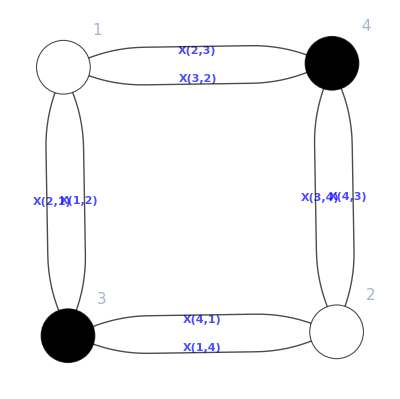

```mathematica
(*SPECIFY WHICH EXAMPLE IT IS*)
ii=71;

(*Below this you don't need to touch*)
formatrule={Subscript[XX_, z1_,z2_]->XX[z1,z2]};
Subscript[bft, ii];
a=a/.formatrule;
b=b/.formatrule;
c=c/.formatrule;
d=d/.formatrule;
topleft=a;
topright=b;
bottomleft=c;
bottomright=d;
viewGraph[a,b,c,d]
```

```mathematica
Subscript[bft, ii];
a=a/.formatrule;
b=b/.formatrule;
c=c/.formatrule;
d=d/.formatrule;

{newa,newb,newc,newd}=collapseBivalentNodes[a,b,c,d];

(*First do the square moves for BFTs*)
squarefaces=Cases[internalFaceLabels[newa,newb,newc,newd],zz_/;Count[Variables[Join[newa,newb,newc,newd]],_[zz,_]|_[_,zz]]==4]
(*Let's do two square moves on the same face and see if we return to the original graph*)
(*doublesquaremoves=Map[collapseBivalentNodes@@squareMove[Sequence@@(collapseBivalentNodes@@squareMove[newa,newb,newc,newd,#,True,True]),#,True,True]&,squarefaces];
*)
newa//MatrixForm
```

{1,2,3,4}

(X[1,2]+X[2,1] | X[2,3]+X[3,2]
X[1,4]+X[4,1] | X[3,4]+X[4,3])

```mathematica
squareMove[topleft_,topright_,bottomleft_,bottomright_,fournodesorfacenum_,BFTgraph_:False,checkneeded_:True]/;(Head[fournodesorfacenum]===Integer&&BFTgraph===True||Head[fournodesorfacenum]===List&&Length[fournodesorfacenum]===4):=Block[{oktoproceed,newtopleft,fournodes,rows,columns,possiblefouredges,edgestosettozero,facenum,positions,duplicateedge,thefacenumber,rowset,columnset,edge4by4,final4by4,whitenodestoadd,blacknodestoadd,newedgeW,newedgeB,ii,biggestindex,newedgesW,newedgesB,newbottomleft,newtopright,newbottomright,findDoubles,doubleedges,replacement,positioninwhichtoreplace,jj},
oktoproceed=True;
If[checkneeded,
oktoproceed=checkKasteleynQ[topleft,topright,bottomleft,bottomright,BFTgraph];
];
If[oktoproceed,
newtopleft=topleft;
(*We only need to manipulate columns and rows in topleft. At the end, we'll also make sure the other parts of the Kasteleyn have the right dimensions*)
If[Head[fournodesorfacenum]===List,
(*the user specified four nodes*)
fournodes=Sort[fournodesorfacenum];
rows=Cases[fournodes,zz_/;zz≤Length[topleft]+Length[bottomleft]];
columns=DeleteCases[fournodes,Alternatives@@rows]-Length[topleft]-Length[bottomleft];
(*This is a list of the possible sets of four edges that link up the four nodes, and hence make a square face (there may be duplicates in this list, but this is irrelevant)*)
possiblefouredges=DeleteCases[Tuples[Map[Variables[topleft[[Sequence@@#]]]&,Tuples[{rows,columns}]]],{___,duplicateedge_,___,duplicateedge_,___}];
(*if we have a BFT graph, we can only choose four edges that all have the same face label*)
If[BFTgraph,
(*we will need to set to zero the four edges that form the square face*)
edgestosettozero=Cases[possiblefouredges,{_[___,thefacenumber_,___],_[___,thefacenumber_,___],_[___,thefacenumber_,___],_[___,thefacenumber_,___]}][[1]];
facenum=(Intersection@@Map[List@@#&,edgestosettozero])[[1]];
positions=Position[topleft,Alternatives@@edgestosettozero];
,edgestosettozero=possiblefouredges[[1]];
];
,(*the user specified a face number*)
facenum=fournodesorfacenum;
positions=Position[topleft,_[facenum,_]|_[_,facenum]];
rows=Union[Map[#[[1]]&,positions]];
columns=Union[Map[#[[2]]&,positions]];
rows=PadRight[rows,2,rows[[1]]];
columns=PadRight[columns,2,columns[[1]]];
edgestosettozero=Map[topleft[[Sequence@@#]]&,positions];
];
If[Length[edgestosettozero]==4,(*we indeed have a 4-edge cycle going between the nodes, and we can do the square move*)
rowset=DeleteDuplicates[rows];
columnset=DeleteDuplicates[columns];
If[BFTgraph,
(*Now we'll kill the connectivity between the four nodes, and introduce four more nodes that are connected with edges bearing the correct index structure (since BFTgraph=True)*)
(*We may have four scenarios: either the connectivity of our square face is such that all variables are in different entries (the most common scenario), i.e. {{X,X},{X,X}}, or we have two rows and one column {{X+X},{X+X}}, or we have one row and two columns {{X+X,X+X}}, or we have one row and one column {{X+X+X+X}}. In each case we need to form a new square with four new nodes, so we'll need to break up the edges in these scenarios to always for a 4x4 matrix. This is easy in the first scenario, but a little trickier in the other scenarios.*)
If[Length[rowset]==2,
If[Length[columnset]==2,
edge4by4=newtopleft[[rowset,columnset]]/.Map[#->0&,Complement[Variables[newtopleft[[rowset,columnset]]],edgestosettozero]];
,edge4by4=Map[Variables,newtopleft[[rowset,columnset]]/.Map[#->0&,Complement[Variables[newtopleft[[rowset,columnset]]],edgestosettozero]]];
edge4by4=edge4by4/.{{{firstedge_[facenum,otherlabel1_],secondedge_},{thirdedge_[facenum,otherlabel2_],fourthedge_}}:>{{firstedge[facenum,otherlabel1],secondedge},{fourthedge,thirdedge[facenum,otherlabel2]}},{{firstedge_[otherlabel1_,facenum],secondedge_},{thirdedge_[otherlabel2_,facenum],fourthedge_}}:>{{firstedge[otherlabel1,facenum],secondedge},{fourthedge,thirdedge[otherlabel2,facenum]}}};
];
,If[Length[columnset]==2,
edge4by4=Map[Variables,Transpose[newtopleft[[rowset,columnset]]]/.Map[#->0&,Complement[Variables[newtopleft[[rowset,columnset]]],edgestosettozero]]];
edge4by4=Transpose[edge4by4/.{{{firstedge_[facenum,otherlabel1_],secondedge_},{thirdedge_[facenum,otherlabel2_],fourthedge_}}:>{{firstedge[facenum,otherlabel1],secondedge},{fourthedge,thirdedge[facenum,otherlabel2]}},{{firstedge_[otherlabel1_,facenum],secondedge_},{thirdedge_[otherlabel2_,facenum],fourthedge_}}:>{{firstedge[otherlabel1,facenum],secondedge},{fourthedge,thirdedge[otherlabel2,facenum]}}}];
,edge4by4=Partition[edgestosettozero,2];
edge4by4=edge4by4/.{{{firstedge_[facenum,otherlabel1_],secondedge_[facenum,otherlabel2_]},{thirdedge_,fourthedge_}}:>{{firstedge[facenum,otherlabel1],fourthedge},{thirdedge,secondedge[facenum,otherlabel2]}},{{firstedge_[otherlabel1_,facenum],secondedge_[otherlabel2_,facenum]},{thirdedge_,fourthedge_}}:>{{firstedge[otherlabel1,facenum],fourthedge},{thirdedge,secondedge[otherlabel2,facenum]}},{{firstedge_[facenum,otherlabel1_],secondedge_},{thirdedge_[facenum,otherlabel2_],fourthedge_}}:>{{firstedge[facenum,otherlabel1],secondedge},{fourthedge,thirdedge[facenum,otherlabel2]}},{{firstedge_[otherlabel1_,facenum],secondedge_},{thirdedge_[otherlabel2_,facenum],fourthedge_}}:>{{firstedge[otherlabel1,facenum],secondedge},{fourthedge,thirdedge[otherlabel2,facenum]}}};
];
];
(*Finally we'll add the connectivity between the new white nodes and the new black nodes*)
final4by4=Transpose[Map[#/.{head_[iij_,jjk_]:>head[jjk,iij]}&,edge4by4,{2}]];
newtopleft[[rowset,columnset]]=newtopleft[[rowset,columnset]]/.Map[#->0&,edgestosettozero];
(*Now we'll add two new rows and two new columns, representing the four new nodes that appear when doing a square move*)
whitenodestoadd=Table[0,{iii,2},{jjj,Dimensions[newtopleft][[2]]}];
blacknodestoadd=Table[{0,0},Length[newtopleft]];
For[ii=1,ii≤2,ii++,
newedgeW=edge4by4[[All,{ii}]]/.{{{_[facenum,iij_]},{_[jjk_,facenum]}}:>XX[jjk,iij],{{_[iij_,facenum]},{_[facenum,jjk_]}}:>XX[iij,jjk]};
whitenodestoadd[[ii,columns[[ii]]]]=newedgeW;
newedgeB=edge4by4[[{ii}]]/.{{{_[facenum,iij_],_[jjk_,facenum]}}:>XX[jjk,iij],{{_[iij_,facenum],_[facenum,jjk_]}}:>XX[iij,jjk]};
blacknodestoadd[[rows[[ii]],ii]]=newedgeB;
];
,(*Since BFTgraph=False we don't have to work so hard with the index structures, i.e. final4by4 is much easier to make.*)
final4by4=Partition[edgestosettozero,2];
newtopleft[[rowset,columnset]]=newtopleft[[rowset,columnset]]/.Map[#->0&,edgestosettozero];
(*Now we'll add two new rows and two new columns, representing the four new nodes that appear when doing a square move*)
whitenodestoadd=Table[0,{iii,2},{jjj,Dimensions[newtopleft][[2]]}];
blacknodestoadd=Table[{0,0},Length[newtopleft]];
(*We'll add edges indexed by an index that hasn't appeared yet, to make sure we don't create duplicate edge names*)
biggestindex=Max[Flatten[Map[List@@#&,Variables[joinupKasteleyn[topleft,topright,bottomleft,bottomright]]]]];
newedgesW=Map[XX[#]&,Range[biggestindex+1,biggestindex+2]];
newedgesB=Map[XX[#]&,Range[biggestindex+3,biggestindex+4]];
For[ii=1,ii≤2,ii++,
whitenodestoadd[[ii,columns[[ii]]]]=newedgesW[[ii]];
blacknodestoadd[[rows[[ii]],ii]]=newedgesB[[ii]];
];
];
newtopleft=Join[Join[newtopleft,whitenodestoadd],Join[blacknodestoadd,final4by4],2];
If[bottomleft==={},
newbottomleft={};
,newbottomleft=Join[bottomleft,Table[0,{iii,Length[bottomleft]},{jjj,2}],2];
];
newtopright=Join[topright,Table[0,{iii,2},{jjj,Dimensions[topright][[2]]}]];
newbottomright=bottomright;
(*Now we're finished. In the event that we created a duplicate edge, we'll rename it by tagging an X onto its Head until it's no longer a duplicate*)
(*This function makes a list of edges that appear twice*)
findDoubles=Function[{aa,bb,cc,dd},
Block[{tempkasteleyn,doubles},
tempkasteleyn=joinupKasteleyn[aa,bb,cc,dd];
doubles=Variables[tempkasteleyn][[Flatten[Position[Map[Length[Position[tempkasteleyn,#]]&,Variables[tempkasteleyn]],z_/;z>1]]]];
doubles]
];
doubleedges=findDoubles[newtopleft,newtopright,newbottomleft,newbottomright];
While[doubleedges=!={},
replacement=Map[(Symbol[StringJoin[SymbolName[Head[#]],"X"]]@@#)&,doubleedges];
positioninwhichtoreplace=Map[Position[newtopleft,#][[1]]&,doubleedges];
For[jj=1,jj≤Length[replacement],jj++,
newtopleft=ReplacePart[newtopleft,positioninwhichtoreplace[[jj]]->replacement[[jj]]];
];
doubleedges=findDoubles[newtopleft,newtopright,newbottomleft,newbottomright];
];
,Print["The square move can only be done on cycles with 4 edges. The current choice is invalid."];
{newtopleft,newtopright,newbottomleft,newbottomright}={Null,Null,Null,Null};
];
,Print["The input Kasteleyn is not valid."];
{newtopleft,newtopright,newbottomleft,newbottomright}={Null,Null,Null,Null};
];
{newtopleft,newtopright,newbottomleft,newbottomright}
];
```

```mathematica
graph=AdjacencyGraph[getAdjacencyMatrix[newa,newb,newc,newd]];
```

```mathematica
allgraphs={graph};
allphases={{newa,newb,newc,newd}};
```

```mathematica
squaremovedphases=Map[collapseBivalentNodes@@squareMove[newa,newb,newc,newd,#,True,True]&,squarefaces];

squaremovedgraphs=Map[AdjacencyGraph[getAdjacencyMatrix[Sequence@@#]]&,squaremovedphases];
Table[IsomorphicGraphQ[allgraphs[[iii]],squaremovedgraphs[[jjj]]],{iii,Length[allgraphs]},{jjj,Length[squaremovedgraphs]}];

(*Now do the square moves for scattering amplitudes*)
Map[Union[#]&,FindCycle[graph,{4},All]/.UndirectedEdge->Sequence];
```

True

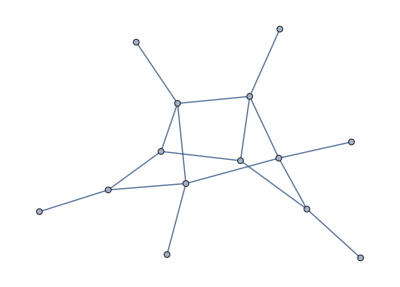

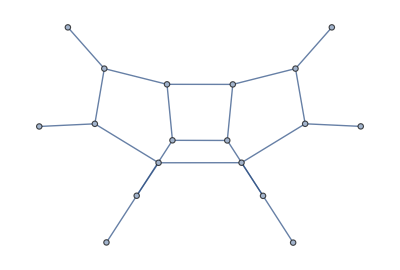

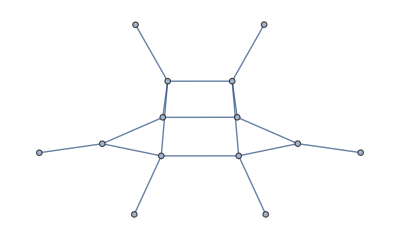

```mathematica
AdjacencyGraph[getAdjacencyMatrix@@{newa,newb,newc,newd}]
AdjacencyGraph[getAdjacencyMatrix@@(collapseBivalentNodes@@squareMove[Sequence@@{newa,newb,newc,newd},2,True,True])]
AdjacencyGraph[getAdjacencyMatrix@@(collapseBivalentNodes@@squareMove[Sequence@@(collapseBivalentNodes@@squareMove[Sequence@@{newa,newb,newc,newd},2,True,True]),2,True,True])]
```

```mathematica
(*Here we are checking the removable edges of Subscript[bft, 29], where there nonPluckerPolesQ returns False at the top-dim level, but returns True after removing a removable edge, e.g. X[1,6].*)
```

```mathematica
ii=29;
If[ii≠33&&ii≠39&&ii≠40&&ii≠50&&ii≠51&&ii≠52,
Print["ii=",ii];
(*If[Mod[ii,10]==0,Print["ii=",ii];
];*)
Subscript[bft, ii];
a=a/.formatrule;
b=b/.formatrule;
c=c/.formatrule;
d=d/.formatrule;

If[Variables[Join[b,c]]=!={},

If[reducibilityQ[a,b,c,d],
thereduction=reductionGraph[a,b,c,d];
{anew,bnew,cnew,dnew}={a,b,c,d}/.Map[#->0&,Last[thereduction]];
hadtoreduce=True;
,{anew,bnew,cnew,dnew}={a,b,c,d};
hadtoreduce=False;
];

removablesscattering=removableEdges[anew,bnew,cnew,dnew,False,False,2];
If[hadtoreduce==False,
removablesgauging1=removableEdges[anew,bnew,cnew,dnew,False,True,1];
];
removablesgauging2=removableEdges[anew,bnew,cnew,dnew,False,True,2];


numsources=Length[findSources[bnew,cnew,perfectMatchings[anew,bnew,cnew,dnew][[1]]]];
numexternalnodes=Length[cnew]+Length[Transpose[bnew]];
maxpossibledimension=numsources(numexternalnodes-numsources);
If[planarityQ[anew,bnew,cnew,dnew]&&polytopeDim[getPmatrix[anew,bnew,cnew,dnew]]==maxpossibledimension,
If[Length[removablesscattering]=!=Length[cnew]+Length[Transpose[bnew]],
Print["ii=",ii," : There's a problem with removableEdges! For a planar diagram there should be as many edges as external nodes"];
];
];

edges=Variables[joinupKasteleyn[anew,bnew,cnew,dnew]];
currentdim=polytopeDim[getPmatrix[anew,bnew,cnew,dnew]];

If[Sort[Cases[Map[#->0&,DeleteCases[DeleteDuplicates[Map[consistentEdgeRemoval[anew,bnew,cnew,dnew,{#},False,True]&,edges]],edges],{2}],zz_/;reducibilityBFTQ[anew/.zz,bnew/.zz,cnew/.zz,dnew]==False&&polytopeDim[getPmatrix[anew/.zz,bnew/.zz,cnew/.zz,dnew]]==currentdim-1]/.Rule->Plus]=!=Sort[removablesgauging2],
Print["ii=",ii," : There's a problem with removableEdges under gauging 2! For a BFT it should be possible to simply use reducibilityBFTQ"];
];

dimscattering=dimensionGrassmannian[anew,bnew,cnew,dnew];

If[Sort[Cases[Map[#->0&,DeleteCases[DeleteDuplicates[Map[consistentEdgeRemoval[anew,bnew,cnew,dnew,{#},False,True]&,edges]],edges],{2}],zz_/;dimensionGrassmannian[anew/.zz,bnew/.zz,cnew/.zz,dnew]===dimscattering-1]/.Rule->Plus]=!=removablesscattering,
Print["ii=",ii," : There's a problem with removableEdges for scattering! The edges don't correspond to those edges which, when removed, reduce the dimension of the Grassmannian by one!"];
];

];
];
```

ii=29

```mathematica
{topleft,topright,bottomleft,bottomright}={anew,bnew,cnew,dnew};
BFTgraph=False;
gauging=2;
```

```mathematica
refpm=X[1,2] X[1,9] X[2,3] X[4,5] X[6,3] X[6,4] X[7,8] X[8,9];
Cmat=pathMatrix[a,b,c,d];

allorder3relations=Map[Equal@@#&,DeleteCases[Map[#/(Intersection@@#)&,Subsets[Map[Times@@#&,Subsets[Map[HoldForm[minor][Sequence@@#]&,Subsets[Range[Dimensions[Cmat][[2]]],{Length[Cmat]}]],{3}]],{2}]]/.Map[HoldForm[minor][Sequence@@#]->0&,Subsets[Range[Dimensions[Cmat][[2]]],{Length[Cmat]}]][[Flatten[Position[minorsAsPerfectMatchings[a/.{X[1,6]->0,X[9,3]->0},b/.{X[1,6]->0,X[9,3]->0},c/.{X[1,6]->0,X[9,3]->0},d],0]]]],{___,0,___}]];
currentpluckerrelations=Map[Simplify,pluckerRelations[Length[Cmat],Dimensions[Cmat][[2]]]/.Map[HoldForm[minor][Sequence@@#]->0&,Subsets[Range[Dimensions[Cmat][[2]]],{Length[Cmat]}]][[Flatten[Position[minorsAsPerfectMatchings[a/.{X[1,6]->0,X[9,3]->0},b/.{X[1,6]->0,X[9,3]->0},c/.{X[1,6]->0,X[9,3]->0},d],0]]]]];
secretorder3relations=DeleteCases[ParallelMap[Simplify,allorder3relations],Alternatives@@currentpluckerrelations];
```

```mathematica
hihi=MapThread[Rule,{Map[HoldForm[minor][Sequence@@#]&,Subsets[Range[Dimensions[Cmat][[2]]],{Length[Cmat]}]],(minorsAsPerfectMatchings[a/.{X[1,6]->0,X[9,3]->0},b/.{X[1,6]->0,X[9,3]->0},c/.{X[1,6]->0,X[9,3]->0},d])}];
numberofsecretrelations=Count[ParallelMap[Expand[#/.hihi]===True&,secretorder3relations],True];
numberofsecretrelations
```

59

```mathematica
refpm=X[1,2] X[1,9] X[2,3] X[4,5] X[6,3] X[6,4] X[7,8] X[8,9];
Cmat=pathMatrix[a/.{X[1,6]->0},b/.{X[1,6]->0},c/.{X[1,6]->0},d];

allorder3relations=Map[Equal@@#&,DeleteCases[Map[#/(Intersection@@#)&,Subsets[Map[Times@@#&,Subsets[Map[HoldForm[minor][Sequence@@#]&,Subsets[Range[Dimensions[Cmat][[2]]],{Length[Cmat]}]],{3}]],{2}]]/.Map[HoldForm[minor][Sequence@@#]->0&,Subsets[Range[Dimensions[Cmat][[2]]],{Length[Cmat]}]][[Flatten[Position[minorsAsPerfectMatchings[a/.{X[1,6]->0},b/.{X[1,6]->0},c/.{X[1,6]->0},d],0]]]],{___,0,___}]];
currentpluckerrelations=Map[Simplify,pluckerRelations[Length[Cmat],Dimensions[Cmat][[2]]]/.Map[HoldForm[minor][Sequence@@#]->0&,Subsets[Range[Dimensions[Cmat][[2]]],{Length[Cmat]}]][[Flatten[Position[minorsAsPerfectMatchings[a/.{X[1,6]->0},b/.{X[1,6]->0},c/.{X[1,6]->0},d],0]]]]];
secretorder3relations=DeleteCases[ParallelMap[Simplify,allorder3relations],Alternatives@@currentpluckerrelations];
```

```mathematica
hihi=MapThread[Rule,{Map[HoldForm[minor][Sequence@@#]&,Subsets[Range[Dimensions[Cmat][[2]]],{Length[Cmat]}]],(minorsAsPerfectMatchings[a/.{X[1,6]->0},b/.{X[1,6]->0},c/.{X[1,6]->0},d])}];
numberofsecretrelations=Count[ParallelMap[Expand[#/.hihi]===True&,secretorder3relations],True];
numberofsecretrelations
```

2

```mathematica
refpm=X[1,2] X[1,9] X[2,3] X[4,5] X[6,3] X[6,4] X[7,8] X[8,9];
Cmat=pathMatrix[a,b,c,d];

allorder3relations=Map[Equal@@#&,DeleteCases[Map[#/(Intersection@@#)&,Subsets[Map[Times@@#&,Subsets[Map[HoldForm[minor][Sequence@@#]&,Subsets[Range[Dimensions[Cmat][[2]]],{Length[Cmat]}]],{3}]],{2}]]/.Map[HoldForm[minor][Sequence@@#]->0&,Subsets[Range[Dimensions[Cmat][[2]]],{Length[Cmat]}]][[Flatten[Position[minorsAsPerfectMatchings[a,b,c,d],0]]]],{___,0,___}]];
currentpluckerrelations=Map[Simplify,pluckerRelations[Length[Cmat],Dimensions[Cmat][[2]]]/.Map[HoldForm[minor][Sequence@@#]->0&,Subsets[Range[Dimensions[Cmat][[2]]],{Length[Cmat]}]][[Flatten[Position[minorsAsPerfectMatchings[a,b,c,d],0]]]]];
secretorder3relations=DeleteCases[ParallelMap[Simplify,allorder3relations],Alternatives@@currentpluckerrelations];
```

```mathematica
hihi=MapThread[Rule,{Map[HoldForm[minor][Sequence@@#]&,Subsets[Range[Dimensions[Cmat][[2]]],{Length[Cmat]}]],(minorsAsPerfectMatchings[a,b,c,d])}];
numberofsecretrelations=Count[ParallelMap[Expand[#/.hihi]===True&,secretorder3relations],True];
numberofsecretrelations
```

0

```mathematica
polytopeDim[getPmatrix[a/.{X[1,6]->0,X[9,3]->0},b/.{X[1,6]->0,X[9,3]->0},c/.{X[1,6]->0,X[9,3]->0},d]]
```

7

```mathematica
dimensionGrassmannian[a/.{X[1,6]->0,X[9,3]->0},b/.{X[1,6]->0,X[9,3]->0},c/.{X[1,6]->0,X[9,3]->0},d]
```

7

```mathematica
nonPluckerPolesQ[a,b,c,d]
```

False

```mathematica
(*Here we are comparing connectivityMatrix with alternativeConnectivityMat*)
```

```mathematica
alternativeConnectivityMat[a_,b_,c_,d_,referencematching_:Null]:=Module[{theperf,adjacencymat,kasteleyn,perfpositions,jj,graph,cyclenodes,turnIntoContributionNothingAdded,cycles,loopnodes,extraloopnodes,toadd,loopcontributions,turnIntoContribution,connectivitymat},
If[referencematching===Null,
theperf=perfectMatchings[a,b,c,d][[lowNumberLoopsPM[a,b,c,d]]];
,theperf=referencematching;
];
adjacencymat=UpperTriangularize[getAdjacencyMatrix[a,b,c,d]];
kasteleyn=joinupKasteleyn[a,b,c,d];
perfpositions=Map[#[[{2,1}]]+{Length[kasteleyn],0}&,Position[kasteleyn,Alternatives@@Variables[theperf]]];
For[jj=1,jj≤Length[perfpositions],jj++,
adjacencymat[[Sequence@@perfpositions[[jj]]]]=1;
adjacencymat[[Sequence@@Reverse[perfpositions[[jj]]]]]=adjacencymat[[Sequence@@Reverse[perfpositions[[jj]]]]]-1;
];

graph=AdjacencyGraph[adjacencymat];

turnIntoContributionNothingAdded=Function[{pathnodes},
Module[{bigmatrix,edges,edgedirections,giveContribution,totalcontrib},
bigmatrix=Join[Join[Table[0,{iii,Length[kasteleyn]},{jjj,Length[kasteleyn]}],Transpose[kasteleyn]],Join[kasteleyn,Table[0,{iii,Dimensions[kasteleyn][[2]]},{jjj,Dimensions[kasteleyn][[2]]}]],2];
edges=Map[bigmatrix[[Sequence@@#]]&,Table[pathnodes[[{iii,iii+1}]],{iii,Length[pathnodes]-1}]];
edgedirections=Map[Ordering[#][[1]]&,Table[pathnodes[[{iii,iii+1}]],{iii,Length[pathnodes]-1}]]/.{2->-1};
giveContribution=Function[{edges,sign},
Block[{contribution},
If[sign==1,
contribution=Total[Intersection[Variables[edges],Complement[Variables[kasteleyn],Variables[theperf]]]];
,contribution=Total[Map[1/#&,Intersection[Variables[edges],Variables[theperf]]]];
];
contribution]
];
totalcontrib=Times@@MapThread[giveContribution[#1,#2]&,{edges,edgedirections}];
totalcontrib
]
];

cycles=FindCycle[graph,Infinity,All]/.{DirectedEdge->List};
loopnodes=Map[#[[Append[Range[1,Length[#],2],Length[#]]]]&,Map[Join@@#&,cycles]];
extraloopnodes={};
For[jj=2,jj≤Length[loopnodes],jj++,
toadd=Cases[Subsets[loopnodes,{jj}],zz_/;Join@@Map[Intersection@@#&,Subsets[zz,{2}]]==={}];
If[toadd==={},
Break[];
];
extraloopnodes=Join[extraloopnodes,toadd];
];
loopnodes=Join[Transpose[{loopnodes}],extraloopnodes];
loopcontributions=Map[Power[-1,Length[#]-1](Times@@#)&,Map[turnIntoContributionNothingAdded,loopnodes,{2}]];
cyclenodes=Map[Union@@#&,loopnodes];

turnIntoContribution=Function[{pathnodes},
Module[{totalcontrib},
totalcontrib=turnIntoContributionNothingAdded[pathnodes];
totalcontrib=totalcontrib/(1-Total[loopcontributions]);
totalcontrib=totalcontrib(1-Total[loopcontributions[[Flatten[Position[Map[Length[Intersection[#,pathnodes]]>0&,cyclenodes],False]]]]]);
totalcontrib
]
];

connectivitymat=Table[FindPath[graph,iii,jjj,Infinity,All],{iii,Total[Dimensions[kasteleyn]]},{jjj,Total[Dimensions[kasteleyn]]}];
connectivitymat=MapThread[Join,{connectivitymat,(DiagonalMatrix[Range[Total[Dimensions[kasteleyn]]]]/.{0->{}})/.{zz_Integer->{{zz}}}},2];
connectivitymat=Map[Total,Map[turnIntoContribution[#]&,connectivitymat,{3}],{2}];
connectivitymat
];
```

```mathematica
alternativetimings={};
normaltimings={};
(*alternativetimings=<<alternativetimings;
normaltimings=<<normaltimings;*)
```

```mathematica
For[ii=1,ii≤76,ii++,
If[ii≠33&&ii≠39&&ii≠50&&ii≠51,
Print["ii=",ii];
(*Below this you don't need to touch*)
formatrule={Subscript[XX_, z1_,z2_]->XX[z1,z2]};
Subscript[bft, ii];
a=a/.formatrule;
b=b/.formatrule;
c=c/.formatrule;
d=d/.formatrule;

perfs=perfectMatchings[a,b,c,d];
srcs=Map[findSources[b,c,#]&,perfs];
multiplic=Map[Tally[srcs][[#,2]]&,Map[Position[Tally[srcs],{#,_}][[1,1]]&,srcs]];

alternative=AbsoluteTiming[alternativeConnectivityMat[a,b,c,d,Null]];
alternativetimings=Append[alternativetimings,{Length[alternative[[2]]],multiplic[[lowNumberLoopsPM[a,b,c,d]]],alternative[[1]]}];
normal=AbsoluteTiming[connectivityMatrix[a,b,c,d,Null]];
normaltimings=Append[normaltimings,{Length[normal[[2]]],multiplic[[lowNumberLoopsPM[a,b,c,d]]],normal[[1]]}];
equals={};
For[jj=1,jj≤Length[perfs],jj++,
If[Mod[jj,10]==0,Print["    jj=",jj];
];
If[multiplic[[jj]]≤3&&jj≠lowNumberLoopsPM[a,b,c,d],
alternative=AbsoluteTiming[alternativeConnectivityMat[a,b,c,d,perfs[[jj]]]];
alternativetimings=Append[alternativetimings,{Length[alternative[[2]]],multiplic[[jj]],alternative[[1]]}];
normal=AbsoluteTiming[connectivityMatrix[a,b,c,d,perfs[[jj]]]];
normaltimings=Append[normaltimings,{Length[normal[[2]]],multiplic[[jj]],normal[[1]]}];
equals=Append[equals,Simplify[alternative[[2]]==normal[[2]]]===True];
];
];
If[And@@equals=!=True,
Print["There is a PROBLEM!!!"];
];
];
];
```

ii=1

ii=2

ii=3

jj=10

ii=4

ii=5

ii=6

jj=10

ii=7

ii=8

ii=9

jj=10

jj=20

ii=10

jj=10

jj=20

jj=30

jj=40

jj=50

ii=11

jj=10

jj=20

ii=12

jj=10

jj=20

jj=30

jj=40

ii=13

jj=10

jj=20

jj=30

jj=40

jj=50

jj=60

jj=70

jj=80

jj=90

jj=100

jj=110

ii=14

jj=10

jj=20

jj=30

jj=40

ii=15

jj=10

jj=20

jj=30

jj=40

ii=16

ii=17

ii=18

ii=19

ii=20

jj=10

ii=21

ii=22

jj=10

ii=23

jj=10

ii=24

jj=10

ii=25

jj=10

jj=20

jj=30

jj=40

jj=50

jj=60

ii=26

jj=10

jj=20

jj=30

jj=40

jj=50

jj=60

jj=70

jj=80

jj=90

jj=100

jj=110

jj=120

jj=130

jj=140

jj=150

jj=160

jj=170

jj=180

jj=190

jj=200

jj=210

jj=220

jj=230

jj=240

jj=250

jj=260

jj=270

jj=280

jj=290

jj=300

jj=310

jj=320

jj=330

jj=340

ii=27

jj=10

jj=20

jj=30

ii=28

jj=10

jj=20

jj=30

jj=40

ii=29

jj=10

jj=20

jj=30

jj=40

ii=30

jj=10

jj=20

jj=30

jj=40

jj=50

jj=60

jj=70

jj=80

ii=31

jj=10

jj=20

jj=30

ii=32

jj=10

jj=20

jj=30

jj=40

jj=50

jj=60

jj=70

jj=80

ii=34

ii=35

ii=36

jj=10

ii=37

jj=10

jj=20

jj=30

ii=38

jj=10

jj=20

jj=30

jj=40

ii=40

jj=10

jj=20

jj=30

jj=40

jj=50

jj=60

ii=41

jj=10

jj=20

jj=30

ii=42

jj=10

jj=20

jj=30

ii=43

jj=10

jj=20

jj=30

jj=40

ii=44

jj=10

jj=20

jj=30

jj=40

ii=45

jj=10

jj=20

jj=30

jj=40

jj=50

jj=60

ii=46

jj=10

jj=20

jj=30

jj=40

jj=50

jj=60

ii=47

jj=10

jj=20

jj=30

jj=40

jj=50

ii=48

jj=10

ii=49

jj=10

ii=52

jj=10

jj=20

jj=30

jj=40

jj=50

jj=60

jj=70

ii=53

jj=10

jj=20

jj=30

jj=40

ii=54

ii=55

ii=56

ii=57

jj=10

jj=20

ii=58

jj=10

jj=20

ii=59

jj=10

jj=20

jj=30

jj=40

ii=60

jj=10

jj=20

jj=30

jj=40

ii=61

jj=10

jj=20

jj=30

jj=40

jj=50

jj=60

jj=70

jj=80

jj=90

jj=100

jj=110

jj=120

jj=130

jj=140

jj=150

jj=160

jj=170

jj=180

jj=190

jj=200

ii=62

jj=10

jj=20

jj=30

jj=40

ii=63

jj=10

jj=20

jj=30

ii=64

jj=10

jj=20

jj=30

ii=65

ii=66

jj=10

ii=67

jj=10

jj=20

ii=68

jj=10

jj=20

jj=30

jj=40

ii=69

jj=10

jj=20

jj=30

jj=40

ii=70

jj=10

ii=71

ii=72

jj=10

ii=73

jj=10

ii=74

jj=10

jj=20

jj=30

jj=40

jj=50

jj=60

ii=75

jj=10

jj=20

jj=30

jj=40

ii=76

jj=10

jj=20

jj=30

jj=40

```mathematica
normaltimings>>normaltimings;
alternativetimings>>alternativetimings;
```

{cc→3.09221}

{cc→2.8752}

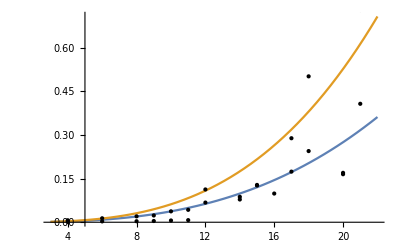

```mathematica
multiplicity=1;
datanormal=Sort[Map[Mean,GatherBy[Map[#[[{1,3}]]&,Cases[normaltimings,{_,multiplicity,_}]],First]]];
dataalternative=Sort[Map[Mean,GatherBy[Map[#[[{1,3}]]&,Cases[alternativetimings,{_,multiplicity,_}]],First]]];
(*ListPlot[{dataalternative,datanormal},PlotRange->All]*)

normalmodel=0.00005(1+(multiplicity-1)0.1465048478811045) xx^cc;
normalfit=Chop[FindFit[datanormal,normalmodel,{cc},xx],10^-6]
normalline=Function[{xx},Evaluate[normalmodel/.normalfit]];

alternativemodel=0.00005(1+(multiplicity-1)0.007644753105478895) xx^cc;
alternativefit=Chop[FindFit[dataalternative,alternativemodel,{cc},xx],10^-6]
alternativeline=Function[{xx},Evaluate[alternativemodel/.alternativefit]];

(*normalmodel=bb xx^cc;
normalfit=Chop[FindFit[datanormal,normalmodel,{bb,cc},xx],10^-6]
alternativemodel=bb xx^cc;
alternativefit=Chop[FindFit[dataalternative,alternativemodel,{bb,cc},xx],10^-6]
Mean[{bb/.normalfit,bb/.alternativefit}]
generalmodel=Mean[{bb/.normalfit,bb/.alternativefit}] xx^cc;
normalfit=Chop[FindFit[datanormal,generalmodel,{cc},xx],10^-6]
alternativefit=Chop[FindFit[dataalternative,generalmodel,{cc},xx],10^-6]
normalline=Function[{xx},Evaluate[generalmodel/.normalfit]];
alternativeline=Function[{xx},Evaluate[generalmodel/.alternativefit]];*)

Plot[{alternativeline[xx],normalline[xx]},{xx,3,22},Epilog->Join[Map[Point[#,VertexColors->Blue]&,dataalternative],Map[Point[#,VertexColors->Orange]&,datanormal]],PlotRange->All]
```

```mathematica
(3.066405674612687+3.3439258526263114+3.655882974069246+3.6219425472110225)/4
(2.843363175648133+2.883866314082025+3.0093816895347447+2.960523322034808)/4
```

3.42204

2.92428

0.146505

0.00764475

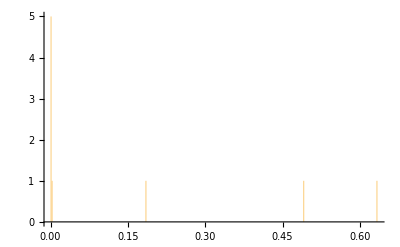

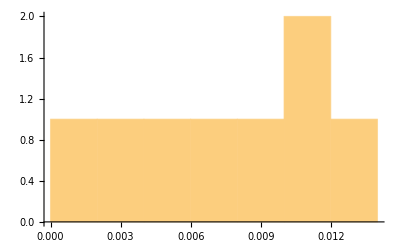

```mathematica
normalgradient={};
alternativegradient={};
For[size=1,size≤24,size++,
datanormal=Sort[Map[Mean,GatherBy[Map[#[[{2,3}]]&,Cases[normaltimings,{size,_,_}]],First]]];
dataalternative=Sort[Map[Mean,GatherBy[Map[#[[{2,3}]]&,Cases[alternativetimings,{size,_,_}]],First]]];
(*ListPlot[{dataalternative,datanormal},PlotRange->All]*)

If[Length[datanormal]≥2,

normalmodel=aa+bb xx;
normalfit=FindFit[datanormal,normalmodel,{aa,bb},xx];
normalgradient=Append[normalgradient,bb/.normalfit];
normalline=Function[{xx},Evaluate[normalmodel/.normalfit]];

alternativemodel=aa+bb xx;
alternativefit=FindFit[dataalternative,alternativemodel,{aa,bb},xx];
alternativegradient=Append[alternativegradient,bb/.alternativefit];
alternativeline=Function[{xx},Evaluate[alternativemodel/.alternativefit]];

(*Print[Plot[{alternativeline[xx],normalline[xx]},{xx,0.5,Max[Transpose[datanormal][[1]]]+0.5},Epilog->Join[Map[Point[#,VertexColors->Blue]&,dataalternative],Map[Point[#,VertexColors->Orange]&,datanormal]],PlotRange->All]];
Print[Last[normalgradient]];*)
];
];
Mean[DeleteCases[normalgradient,zz_/;zz>2Median[normalgradient]]]
Mean[DeleteCases[alternativegradient,zz_/;zz>2Median[alternativegradient]]]
Histogram[DeleteCases[normalgradient,zz_/;zz>2Median[normalgradient]],200]
Histogram[DeleteCases[alternativegradient,zz_/;zz>2Median[alternativegradient]],6]
```

```mathematica
(*THIS IS THE TIME IT TAKES FOR A COMPUTATION!*)
finalmodelNORMAL[size_,multiplicity_]:=0.00005(1+(multiplicity-1)0.1465048478811045) size^3.422039262129817;
(*finalmodelNORMAL[size_,multiplicity_]:=0.00005(1+(multiplicity-1)0.4965048478811045) size^3.402039262129817;*)
finalmodelALTERNATIVE[size_,multiplicity_]:=0.00005(1+(multiplicity-1)0.007644753105478895) size^2.924283625324928;

Mean[Map[finalmodelNORMAL[#[[1]],#[[2]]]-#[[3]]&,normaltimings]]
Mean[Map[Abs[finalmodelNORMAL[#[[1]],#[[2]]]-#[[3]]]&,normaltimings]]
Mean[Map[finalmodelALTERNATIVE[#[[1]],#[[2]]]-#[[3]]&,alternativetimings]]
Mean[Map[Abs[finalmodelALTERNATIVE[#[[1]],#[[2]]]-#[[3]]]&,alternativetimings]]
```

-3.04997

3.58308

-0.188793

0.188793

```mathematica
FindMinimum[Mean[Map[Abs[(0.0000023(1+(#[[2]]-1)multcoeff) (#[[1]])^exponent)-#[[3]]]&,normaltimings]],{{multcoeff,0.1465048478811045},{exponent,3.422039262129817}}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{3.25033,{multcoeff→120.203,exponent→2.91427}}

```mathematica
FindMinimum[Mean[Map[Abs[(0.000023(1+(#[[2]]-1)multcoeff) (#[[1]])^exponent)-#[[3]]]&,alternativetimings]],{{multcoeff,0.007644753105478895},{exponent,2.924283625324928}}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.0571947,{multcoeff→0.356511,exponent→3.07294}}

```mathematica
loadupnormal=<<normaltimings;
loadupalternative=<<alternativetimings;
```

```mathematica
FindMinimum[Mean[Map[Abs[(0.0000023(1+(#[[2]]-1)multcoeff) (#[[1]])^exponent)-#[[3]]]&,loadupnormal]],{{multcoeff,0.1465048478811045},{exponent,3.422039262129817}}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{3.06266,{multcoeff→194.422,exponent→2.71977}}

```mathematica
FindMinimum[Mean[Map[Abs[(0.000023(1+(#[[2]]-1)multcoeff) (#[[1]])^exponent)-#[[3]]]&,loadupalternative]],{{multcoeff,0.007644753105478895},{exponent,2.924283625324928}}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.0561878,{multcoeff→0.359089,exponent→3.0413}}

```mathematica
FindMinimum[Mean[Map[Abs[(0.0000023(1+(#[[2]]-1)multcoeff) (#[[1]])^exponent)-#[[3]]]&,Join[normaltimings,loadupnormal]]],{{multcoeff,0.1465048478811045},{exponent,3.422039262129817}}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{3.15735,{multcoeff→124.908,exponent→2.88826}}

```mathematica
FindMinimum[Mean[Map[Abs[(0.000023(1+(#[[2]]-1)multcoeff) (#[[1]])^exponent)-#[[3]]]&,Join[alternativetimings,loadupalternative]]],{{multcoeff,0.007644753105478895},{exponent,2.924283625324928}}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.0570451,{multcoeff→0.351048,exponent→3.06163}}

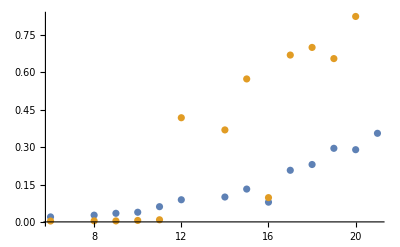

```mathematica
getmean[list_]:=Map[Mean,GatherBy[DeleteCases[Map[#[[{1,3}]]&,Cases[list,{_,2,_}]],zz_/;Last[zz]>1],First]];
ListPlot[{getmean[alternativetimings],getmean[normaltimings]},PlotRange->All]
```